## Modeling Gene Expression with LacI

### Importing Data and Setting Plotting Styles

#### Data

Each entry is in the form 
{Distal Operator, -35 element, -10 element, Proximal Operator, Gene Expression without IPTG, Gene Expression with 1mM IPTG}

```mathematica
data={{"O2_leftSym","minus35_31A_32C","minus10_7A","lacO2",1.58109221329789,2.26921534955135},{"O3_rightSym","minus35_33T","minus10_12G","O1_rightSym",0.9321933744682,1.02580460758288},{"lacOsym","minus35_30C_33T","minus10cons","lacOsym",0.474487606947654,0.796496794576111},{"lacOsym","minus35cons","minus10cons","O3_leftSym",6.03335198330537,9.5074375416862},{"lacO3","minus35_30C_33T","minus10_12A","O3_rightSym",2.08422037608823,1.2184346731574},{"O3_rightSym","minus35_31A_32C","minus10_12G","O3_rightSym",0.640054273313486,0.988582615286843},{"O1_rightSym","minus35_33T","minus10_12G","O3_rightSym",0.826064608652993,0.864793134321912},{"lacO1","minus35_31A_32C","minus10_7A","lacOscram",1.36705550655562,1.4113524366962},{"O3_rightSym","minus35_31A_32C","minus10_12A","lacOsym",0.951150119254804,0.298244142975826},{"O3_rightSym","minus35_31A_32C","minus10_12A","O1_rightSym",1.08811415407918,0.85066640565099},{"O3_rightSym","minus35_31A_32C","minus10_12G","lacO2",2.75238982648545,2.3637811598395},{"O1_rightSym","minus35cons","minus10_12A","O2_rightSym",1.12304895429101,1.35469338523993},{"lacOscram","minus35_31A_32C","minus10cons","O2_rightSym",4.81744185468305,12.6749181165155},{"lacOsym","minus35cons","minus10_12G","O3_rightSym",4.19695285717002,4.60318979443721},{"O2_leftSym","minus35_31A_32C","minus10_12A","lacO1",1.61541574624095,1.4746611536348},{"lacO3","minus35_31A_32C","minus10_7A","O1_rightSym",0.775810274790858,1.25878062300825},{"O3_rightSym","minus35_31A_32C","minus10_12G","lacOscram",0.970331789948468,0.70503509878548},{"O3_leftSym","minus35cons","minus10_7A","lacO3",9.03891615022255,6.00490619828081},{"O1_rightSym","minus35_33T","minus10_12A","lacO1",1.38867912450533,1.47615563886919},{"lacOscram","minus35cons","minus10_12G","O1_rightSym",5.8515332179899,6.66679466246815},{"lacO3","minus35_31A_32C","minus10_12G","O1_rightSym",1.27879184424935,1.19786551837456},{"lacOscram","minus35_33T","minus10_12A","O3_rightSym",1.49028196695253,1.78689841193134},{"O3_rightSym","minus35cons","minus10_12A","lacO3",9.755786293191,8.56183130796378},{"O2_leftSym","minus35cons","minus10_12G","lacO3",5.89690813408253,5.09411332436398},{"O3_leftSym","minus35_30C_33T","minus10cons","lacOsym",0.595748351103934,1.20215201990054},{"lacOsym","minus35_33T","minus10_12A","lacOsym",1.8144821553746,1.02606781186484},{"O3_leftSym","minus35_30C_33T","minus10cons","lacO3",1.89958033403741,2.2260117995056},{"O1_rightSym","minus35_30C_33T","minus10_7A","O1_rightSym",0.925767684135862,0.982908346214747},{"lacOscram","minus35_31A_32C","minus10_12A","lacO3",1.21569074083538,1.45616534496643},{"O1_rightSym","minus35cons","minus10_12G","lacOscram",2.49167534152514,2.80487869349346},{"lacO3","minus35_31A_32C","minus10_12G","lacOsym",2.76291518874111,1.05980192371924},{"lacOsym","minus35_31A_32C","minus10_12G","lacO2",1.65389937977279,1.44266337311959},{"O1_rightSym","minus35cons","minus10_12A","O2_leftSym",2.7045887031157,3.75569149187692},{"lacOsym","minus35cons","minus10cons","O1_rightSym",3.65804053752053,15.3979383003769},{"O3_rightSym","minus35cons","minus10_12G","O2_rightSym",7.70803990819353,8.09632437902117},{"lacOsym","minus35_30C_33T","minus10_12A","O2_leftSym",1.17180340911945,1.74934830807386},{"lacO1","minus35_30C_33T","minus10_12G","lacO1",0.7964105331712,1.28970830808765},{"O3_rightSym","minus35_30C_33T","minus10_12A","O3_leftSym",1.06867520979656,0.749645272555175},{"O3_rightSym","minus35cons","minus10_12G","lacO3",9.20382094655919,10.3752581154825},{"lacOscram","minus35_30C_33T","minus10_12A","O2_leftSym",0.863319407576943,0.593327652402166},{"lacO3","minus35_30C_33T","minus10cons","O2_leftSym",0.5413891987586,0.610620460366126},{"lacO2","minus35_31A_32C","minus10_12A","lacOscram",0.786761176909707,1.12444445187937},{"lacO1","minus35_33T","minus10_7A","O3_leftSym",0.805655920081119,0.959129857544084},{"O2_leftSym","minus35_31A_32C","minus10_7A","O3_rightSym",2.61576506620979,1.51909894209615},{"lacO1","minus35_30C_33T","minus10_12G","O2_leftSym",1.01285637308475,1.11552626873821},{"O1_rightSym","minus35_30C_33T","minus10_7A","lacO3",1.33030617730427,0.744404147044965},{"lacO1","minus35_31A_32C","minus10cons","lacO1",3.41333298037555,25.0876136584661},{"O2_leftSym","minus35_33T","minus10_12G","O2_rightSym",0.49634110913001,0.414213587770517},{"lacOsym","minus35_31A_32C","minus10_7A","lacOscram",0.432159169516222,0.750968438354032},{"lacOscram","minus35cons","minus10_12G","O3_leftSym",7.41716484887499,12.8153910708498},{"O3_leftSym","minus35_33T","minus10_12A","lacO2",2.47524289267482,1.36556490331991},{"O3_leftSym","minus35cons","minus10_7A","O2_leftSym",1.78653506226568,3.71957781344211},{"O2_rightSym","minus35_33T","minus10_7A","O2_rightSym",0.704566134182536,1.35721821525304},{"O1_rightSym","minus35_33T","minus10_12A","O3_rightSym",1.31612717163578,1.09910083680671},{"lacOsym","minus35_30C_33T","minus10_12G","O3_leftSym",1.88204025774273,1.33292266639011},{"O2_rightSym","minus35_30C_33T","minus10_12A","O3_rightSym",0.735505126808231,0.523933228130892},{"O1_rightSym","minus35_31A_32C","minus10_12A","lacOscram",1.14130859195703,0.898460483775702},{"O3_leftSym","minus35cons","minus10cons","O3_leftSym",30.3300556321355,32.1408088627689},{"lacO1","minus35_31A_32C","minus10_12A","lacOsym",1.9884346604845,1.36993226910872},{"lacOsym","minus35cons","minus10cons","lacO3",3.20426358904067,18.1311775658982},{"lacO2","minus35_33T","minus10cons","lacOscram",3.50046288102197,4.74556102530628},{"lacOsym","minus35_30C_33T","minus10cons","O3_rightSym",2.18696430127559,2.18253137325378},{"O2_leftSym","minus35_30C_33T","minus10_7A","lacO2",0.645155480784348,1.01034475921693},{"lacO3","minus35_30C_33T","minus10_12A","lacO1",2.41470469311804,2.85861767345371},{"lacOsym","minus35_33T","minus10_7A","lacO3",2.19723823438507,2.40319876658739},{"O3_rightSym","minus35_30C_33T","minus10_12A","O1_rightSym",0.886664098839029,0.655911544338175},{"O2_rightSym","minus35cons","minus10_12G","lacO3",2.5390720228327,3.50980593491635},{"O3_leftSym","minus35_33T","minus10_12A","O3_rightSym",0.771719552497524,0.714035699226415},{"lacOsym","minus35_33T","minus10_7A","lacOsym",0.778320959530394,0.773239195828878},{"O2_rightSym","minus35_30C_33T","minus10cons","O2_leftSym",2.18799287920882,1.7506050640855},{"O1_rightSym","minus35_31A_32C","minus10_7A","lacOsym",0.395171882281694,0.818475739410614},{"lacO2","minus35_31A_32C","minus10_12A","O3_leftSym",1.11460654694669,0.736801992569509},{"lacO3","minus35_30C_33T","minus10cons","lacO2",1.04677405878669,1.31648182544188},{"O3_leftSym","minus35_31A_32C","minus10_12G","lacO2",1.09657961207933,1.17711174490853},{"lacO1","minus35_31A_32C","minus10_12A","O1_rightSym",0.662087324867196,0.352994507011812},{"O2_leftSym","minus35_31A_32C","minus10cons","lacOscram",12.4953498590263,12.4567646201076},{"O3_rightSym","minus35cons","minus10cons","lacOsym",1.9483504182731,15.7578426816585},{"O3_leftSym","minus35cons","minus10_12G","lacO3",6.23099337471862,7.77113388436702},{"O3_leftSym","minus35cons","minus10_7A","O3_leftSym",5.55279014435335,3.62358085827927},{"lacO1","minus35_31A_32C","minus10_12G","O2_leftSym",1.27990625631985,1.04366598270679},{"O3_rightSym","minus35_33T","minus10_12A","lacO3",0.941409516475406,1.9395598438023},{"lacO3","minus35_30C_33T","minus10_12A","O2_leftSym",0.62244038426099,0.637117428793384},{"lacO2","minus35_31A_32C","minus10_12G","O2_leftSym",1.08744281863723,2.0361415413124},{"O1_rightSym","minus35_31A_32C","minus10_12G","lacO3",0.969132661387484,1.28852195729227},{"O3_leftSym","minus35_30C_33T","minus10_12A","O2_rightSym",0.580331069118026,0.644835934331068},{"O2_leftSym","minus35cons","minus10_12G","lacOscram",1.70682181917405,1.80932918766708},{"O2_rightSym","minus35_33T","minus10_7A","lacO1",0.759106407080845,1.69654615525988},{"lacOsym","minus35cons","minus10_12A","lacO2",3.36680625923229,1.82818172163321},{"O3_rightSym","minus35_30C_33T","minus10_12G","O3_leftSym",1.11412602688297,0.932283856013781},{"lacOscram","minus35_33T","minus10_12A","lacOscram",1.46165274564258,0.820060061884432},{"O3_leftSym","minus35_31A_32C","minus10_7A","O2_rightSym",1.34127235576862,1.64446410678298},{"lacOscram","minus35cons","minus10_12G","lacO3",10.2340120167341,14.2867263188587},{"lacOscram","minus35cons","minus10_7A","lacO3",4.19030760094167,4.46116501423227},{"lacO2","minus35_33T","minus10_7A","O3_rightSym",1.11528514777182,0.79217983243723},{"lacOsym","minus35cons","minus10_12G","O2_leftSym",4.61967317077171,8.37582061398883},{"O3_leftSym","minus35_30C_33T","minus10cons","lacO1",1.35648543513683,3.55902536293628},{"O2_leftSym","minus35_31A_32C","minus10_12A","O3_rightSym",1.26224111059346,1.01979740716084},{"lacO2","minus35_33T","minus10_7A","O2_leftSym",0.953851053992298,1.01599684283772},{"O2_leftSym","minus35_33T","minus10_7A","O3_rightSym",1.43673334935952,1.38109998788765},{"lacO3","minus35cons","minus10_12A","lacOscram",1.86246581547256,1.90646930473207},{"lacOscram","minus35cons","minus10_12A","O3_leftSym",3.32922986891477,3.22958478959089},{"O3_leftSym","minus35_31A_32C","minus10_7A","lacOscram",1.50996331935034,1.85269280319437},{"O2_leftSym","minus35_33T","minus10_12A","O3_leftSym",1.70892150247569,1.31649072952423},{"lacOsym","minus35_33T","minus10_7A","lacO1",1.15227343530649,1.28793613473986},{"lacO1","minus35_33T","minus10_12A","lacOsym",0.737456793465848,0.563037469045184},{"O2_rightSym","minus35cons","minus10_7A","O3_leftSym",6.4526226339593,9.36248542032006},{"O2_rightSym","minus35_30C_33T","minus10cons","O3_leftSym",0.895045975136509,0.817641951488903},{"lacO3","minus35_33T","minus10_12G","O2_rightSym",0.528878893526136,0.753688613631364},{"lacO2","minus35cons","minus10cons","O2_leftSym",36.6769348764266,28.3398611030083},{"lacO1","minus35_31A_32C","minus10cons","lacO2",13.0380885550875,31.0639786302605},{"O1_rightSym","minus35_33T","minus10_7A","O2_rightSym",1.20130211201471,1.14021688605031},{"lacO3","minus35_30C_33T","minus10_7A","O2_rightSym",1.10280182023618,0.896021109601736},{"O3_rightSym","minus35_31A_32C","minus10cons","O2_rightSym",3.80302954822356,3.35187491079376},{"O2_leftSym","minus35cons","minus10cons","O1_rightSym",70.1715644862544,72.5391161249404},{"lacOscram","minus35_31A_32C","minus10_7A","O1_rightSym",1.34095533800027,0.949864653874509},{"O3_rightSym","minus35_30C_33T","minus10_7A","O2_leftSym",1.03030058252693,1.09375618681653},{"O3_rightSym","minus35cons","minus10_12A","O2_rightSym",2.00495555194935,1.85454666001158},{"O2_rightSym","minus35_33T","minus10_12G","lacOscram",0.801487626302363,1.17326970611762},{"lacOsym","minus35cons","minus10cons","lacO1",2.24443481698882,39.6744819938818},{"lacOscram","minus35_33T","minus10cons","lacO2",4.58475676324191,3.50170197190298},{"lacO1","minus35_30C_33T","minus10_12A","lacO3",1.19030534165944,1.34063794632241},{"lacO2","minus35_30C_33T","minus10_7A","O2_rightSym",1.46170591347905,1.03475098015393},{"O2_rightSym","minus35cons","minus10_7A","lacOscram",5.57926645117163,4.91759089297179},{"lacO1","minus35_31A_32C","minus10cons","lacO3",2.16836111458909,10.7090731123785},{"lacOsym","minus35_30C_33T","minus10_12A","lacO3",1.08977727366387,1.42703057934762},{"O2_leftSym","minus35cons","minus10_7A","O1_rightSym",11.4303652524168,6.93196740394405},{"O2_leftSym","minus35cons","minus10_7A","lacOscram",7.10836021089367,5.59304586442551},{"O3_leftSym","minus35_31A_32C","minus10_7A","lacO2",1.34650153360337,1.60735714245505},{"O2_leftSym","minus35cons","minus10_12A","O2_rightSym",5.74820976655475,5.13604708163427},{"O3_leftSym","minus35cons","minus10_12G","lacO1",1.41124453023739,4.08280602761852},{"O2_leftSym","minus35_33T","minus10cons","lacO2",10.5638698482069,12.9539269884201},{"lacOscram","minus35_30C_33T","minus10_12G","O1_rightSym",1.09581093214172,0.972544386117639},{"O2_leftSym","minus35_31A_32C","minus10_12G","lacO2",3.0624490938234,2.41650366056018},{"O3_leftSym","minus35cons","minus10_12G","lacO2",10.7876044222414,13.9007828734878},{"lacO1","minus35cons","minus10_12A","lacO1",0.834943756499501,1.75212831154445},{"O3_leftSym","minus35_33T","minus10_12G","lacOsym",1.01395596719409,0.803806179634531},{"O2_leftSym","minus35_33T","minus10_7A","O3_leftSym",1.43035805818525,1.52790163911795},{"O1_rightSym","minus35_33T","minus10_7A","lacOscram",2.87626346545806,2.98331179079551},{"lacO3","minus35_31A_32C","minus10_12A","O2_rightSym",1.34813126457618,0.682698845836531},{"O3_leftSym","minus35cons","minus10_12G","O2_leftSym",2.9558737141872,3.63940959034919},{"O3_leftSym","minus35_33T","minus10_7A","lacO1",0.935766885072036,1.14763656616801},{"O2_rightSym","minus35_33T","minus10_12A","O2_rightSym",1.48798644351376,0.930090696641823},{"lacOscram","minus35_30C_33T","minus10cons","lacO2",2.31371531325267,1.92203460134526},{"lacO1","minus35_33T","minus10cons","lacO3",3.5264321262177,6.54573510027777},{"lacO1","minus35cons","minus10_12G","lacO3",1.62611439573447,1.82900911580256},{"lacO2","minus35_31A_32C","minus10_12G","lacOscram",1.38477814010754,1.50417110197772},{"lacO2","minus35_30C_33T","minus10cons","lacOsym",1.62091402068421,2.26047161169098},{"lacOscram","minus35_31A_32C","minus10_7A","lacO2",0.688273389104621,0.761043537001385},{"O1_rightSym","minus35cons","minus10cons","O2_rightSym",18.3942667351634,25.208492712872},{"lacOscram","minus35_30C_33T","minus10_12A","lacOscram",0.883434470857188,0.757636049676279},{"lacO2","minus35_31A_32C","minus10cons","lacOsym",0.740910330067467,3.87483316297194},{"lacO1","minus35_31A_32C","minus10_12A","lacO1",0.597003220099468,1.12795529536618},{"O3_leftSym","minus35_33T","minus10cons","O3_rightSym",5.31630368550103,5.24431221255611},{"lacO2","minus35_30C_33T","minus10_12G","lacO3",1.31974747710135,0.476257189521718},{"O2_leftSym","minus35_31A_32C","minus10_7A","lacO3",1.57183165005496,1.5807772860404},{"O1_rightSym","minus35_33T","minus10_12A","lacO3",2.37962434907672,0.898277260004611},{"lacO1","minus35_31A_32C","minus10cons","O2_leftSym",8.17774245834775,10.521580517627},{"O2_rightSym","minus35_30C_33T","minus10_7A","O1_rightSym",0.601524530982505,0.341671141959672},{"lacO1","minus35_31A_32C","minus10_12G","O3_leftSym",1.27905865615112,1.14981773365275},{"O2_rightSym","minus35_30C_33T","minus10_12A","O2_leftSym",0.521526966928809,0.670983898901766},{"lacOsym","minus35_33T","minus10cons","lacO1",0.736032535925429,2.52031680911412},{"O2_rightSym","minus35_33T","minus10cons","O2_rightSym",2.30205411422276,4.62703621171108},{"lacO2","minus35_31A_32C","minus10_12G","O3_leftSym",1.40850806254651,1.21628837359914},{"O3_leftSym","minus35cons","minus10_12A","lacOsym",0.545662625776984,1.58395045064905},{"lacOsym","minus35_33T","minus10_12G","O1_rightSym",1.72155363233911,1.29679484130652},{"lacOsym","minus35_33T","minus10_7A","lacO2",0.884305255872891,0.914937514776911},{"lacOsym","minus35_33T","minus10_12A","lacO1",1.36395011796479,0.93074843974902},{"O3_rightSym","minus35_33T","minus10_7A","lacOscram",1.57789701915195,1.57019587858579},{"O3_leftSym","minus35_30C_33T","minus10cons","O3_leftSym",0.985564588136113,1.1215617651736},{"lacO3","minus35cons","minus10cons","lacO1",9.96550861656202,46.0214001234002},{"O2_leftSym","minus35_33T","minus10cons","O2_rightSym",25.6531034061989,39.876024712913},{"lacO1","minus35_33T","minus10_12A","O3_leftSym",1.18680018473983,0.669704325855702},{"O3_leftSym","minus35_33T","minus10_12G","lacOscram",1.10289880570703,0.879509503416323},{"O3_rightSym","minus35_33T","minus10_12A","O3_leftSym",1.00630404431014,1.02056099638442},{"O3_rightSym","minus35cons","minus10_12A","O3_rightSym",0.807470769613017,1.01107411741246},{"O3_leftSym","minus35_31A_32C","minus10_12A","lacOsym",1.31497945486257,1.2807421567776},{"lacO3","minus35_30C_33T","minus10_12A","O2_rightSym",0.417202556111903,0.688823248737567},{"O3_leftSym","minus35cons","minus10cons","lacOscram",21.7802635362836,25.9418029351693},{"lacO2","minus35_33T","minus10_12A","O3_leftSym",0.954384211701783,0.521800544396552},{"lacO3","minus35cons","minus10_7A","O2_rightSym",2.84330531328625,6.1668479045189},{"O3_leftSym","minus35cons","minus10cons","lacOsym",3.84285671558388,26.0713902117742},{"O3_rightSym","minus35_33T","minus10_7A","O2_leftSym",1.03878076155025,1.09114153206679},{"lacOscram","minus35_33T","minus10cons","lacO1",2.50870063518551,6.23267166629062},{"O2_rightSym","minus35cons","minus10cons","O3_leftSym",10.5504106483132,15.9992387608756},{"lacO3","minus35_33T","minus10cons","lacO2",2.81207930591258,3.08261579011739},{"O3_leftSym","minus35cons","minus10_7A","lacOscram",4.12617254249254,3.8768262505681},{"lacOsym","minus35_30C_33T","minus10_12G","lacO1",1.70890345195741,1.67779211349662},{"lacO3","minus35_30C_33T","minus10_7A","O2_leftSym",0.51021230356292,0.708063653310176},{"O2_rightSym","minus35_31A_32C","minus10_7A","lacOsym",1.26002951278258,0.885042066950062},{"lacO1","minus35cons","minus10_7A","lacO2",7.2188294615895,7.93853596700105},{"lacOsym","minus35_33T","minus10_12G","lacO2",0.560584008944592,1.27904958662178},{"lacO2","minus35_31A_32C","minus10cons","O1_rightSym",42.5321317153018,37.9327434296694},{"O3_rightSym","minus35_33T","minus10_12A","lacOsym",0.50496194810346,0.615097034961679},{"lacOscram","minus35cons","minus10cons","O1_rightSym",15.8567235856626,34.1994511565044},{"lacO1","minus35_33T","minus10_12A","O2_rightSym",1.46543533915307,0.905050095646914},{"O1_rightSym","minus35_33T","minus10_7A","O3_rightSym",0.489029771156144,0.461555389641167},{"O1_rightSym","minus35_31A_32C","minus10_7A","O2_leftSym",1.2500758727068,1.28758432621817},{"O1_rightSym","minus35_30C_33T","minus10_12A","O2_rightSym",0.827029268231323,0.698048055750697},{"O3_leftSym","minus35_33T","minus10_12G","O2_rightSym",1.45968573061172,1.47320085278488},{"O3_rightSym","minus35_31A_32C","minus10_12G","O2_rightSym",0.576943426113534,1.52716396576765},{"lacOsym","minus35_31A_32C","minus10_12G","lacO1",0.796988277026933,1.26982438089054},{"lacOsym","minus35_31A_32C","minus10_12A","O2_rightSym",0.759692017431576,1.06596294819519},{"O3_leftSym","minus35_31A_32C","minus10cons","O1_rightSym",15.6907324271938,17.4996962761831},{"O1_rightSym","minus35_30C_33T","minus10_12G","lacO3",0.774850251660925,0.830986867112614},{"O3_rightSym","minus35_33T","minus10_7A","O3_rightSym",2.16242149615,0.732492973387619},{"O1_rightSym","minus35_31A_32C","minus10_12G","lacOscram",1.84335145720152,1.96572681813026},{"lacO1","minus35_30C_33T","minus10_12A","O3_rightSym",0.821909049918382,1.15337321565156},{"O1_rightSym","minus35cons","minus10_12A","lacO3",2.30088757336683,2.5329693152483},{"O3_leftSym","minus35_30C_33T","minus10_12G","O2_rightSym",0.528233195207342,0.673104864034163},{"lacOsym","minus35_30C_33T","minus10cons","lacO1",1.05626590660073,3.46257692949354},{"lacO2","minus35_31A_32C","minus10_7A","lacOsym",0.91162710284842,1.16145761466105},{"O1_rightSym","minus35_30C_33T","minus10_7A","O2_rightSym",1.24878048213126,0.974364364749094},{"lacO3","minus35cons","minus10cons","O2_rightSym",32.8576812297088,25.6996473716197},{"O3_leftSym","minus35cons","minus10_12G","O3_rightSym",2.3667596414712,2.56174478946369},{"O3_rightSym","minus35_31A_32C","minus10_12A","O3_rightSym",1.79713724595223,2.05805773863025},{"O3_leftSym","minus35_31A_32C","minus10_12A","lacO3",1.38396471228515,1.53822708717799},{"O1_rightSym","minus35cons","minus10_7A","O2_leftSym",6.94475438253163,7.55598523640287},{"O2_rightSym","minus35cons","minus10_7A","lacOsym",0.9720257363389,3.38595052086466},{"O1_rightSym","minus35cons","minus10cons","lacOsym",1.7153261389605,14.9263403430468},{"O2_leftSym","minus35cons","minus10_12G","O1_rightSym",5.04726094121607,5.81156954732074},{"lacOsym","minus35_31A_32C","minus10_12G","lacOscram",0.610686711516776,0.817537729328835},{"lacOsym","minus35_31A_32C","minus10_12A","O2_leftSym",0.832910995216509,0.822751191737159},{"O3_rightSym","minus35_33T","minus10cons","lacO1",1.36095197737961,5.95537061166087},{"lacO2","minus35_33T","minus10_12A","lacO1",1.3673565487658,0.758778226752439},{"lacO3","minus35cons","minus10_12A","O3_rightSym",2.51169245125307,2.90633819126087},{"lacOsym","minus35cons","minus10_12G","O3_leftSym",1.20490931593219,2.87944508562687},{"lacO1","minus35_33T","minus10_12G","O3_rightSym",1.19271554103779,1.37889294744978},{"O2_leftSym","minus35_30C_33T","minus10_12A","lacOsym",1.20451572522332,0.416878158135136},{"lacO3","minus35_30C_33T","minus10_12A","lacO3",0.550251376807921,0.684807313431127},{"lacOscram","minus35_30C_33T","minus10cons","lacO1",2.26946577292142,2.72926221178599},{"lacO1","minus35_30C_33T","minus10_12G","O1_rightSym",0.617474865663179,0.490192612763338},{"lacO2","minus35_31A_32C","minus10_12A","O3_rightSym",1.21971735739876,1.09390438438321},{"lacOscram","minus35_31A_32C","minus10cons","lacOsym",1.87043208526028,11.6012080096775},{"O2_rightSym","minus35_33T","minus10_7A","lacO3",1.74155410371288,1.84994866280014},{"O2_rightSym","minus35_30C_33T","minus10cons","lacO3",1.13114352196437,1.2200680558509},{"lacO2","minus35_31A_32C","minus10_12G","lacO1",0.605360223709413,1.11501201656401},{"O2_rightSym","minus35_30C_33T","minus10cons","lacO2",0.924705010991235,1.37224209565949},{"O1_rightSym","minus35_31A_32C","minus10_12G","lacOsym",1.55106839802349,1.64537350735783},{"lacO2","minus35cons","minus10cons","O2_rightSym",35.7114007707435,46.9488308848661},{"lacO2","minus35_33T","minus10_12A","O2_rightSym",1.61220620793322,2.97664366159654},{"lacO1","minus35_30C_33T","minus10_12G","O3_leftSym",1.66712605799635,1.03122889012733},{"lacO1","minus35_30C_33T","minus10_7A","O2_rightSym",0.616213898691283,0.822928223750384},{"O1_rightSym","minus35_31A_32C","minus10_12G","lacO2",2.05117831145891,1.81189802846995},{"lacO2","minus35_30C_33T","minus10_12A","lacO1",0.604622152300223,0.631739027672181},{"lacO2","minus35cons","minus10_7A","O2_leftSym",3.87334367362183,4.47510916576171},{"O3_leftSym","minus35cons","minus10cons","O2_rightSym",21.4828213812532,24.3609455508958},{"lacOscram","minus35_30C_33T","minus10cons","O2_rightSym",3.46290667721003,3.60988957178628},{"lacOscram","minus35_31A_32C","minus10_12A","lacO2",0.992205523503173,0.913275354666313},{"lacOscram","minus35_33T","minus10_7A","O2_rightSym",1.19835998480247,1.63313058831507},{"lacO3","minus35cons","minus10_12G","lacOsym",3.79094805382432,8.88944280562257},{"O2_rightSym","minus35_30C_33T","minus10_7A","lacOscram",1.20443632730753,0.917843736770463},{"O2_rightSym","minus35_33T","minus10_12A","O3_rightSym",1.45685008283195,1.28860207411732},{"O2_leftSym","minus35_33T","minus10_7A","O2_leftSym",2.17722436682508,1.67666165619379},{"O1_rightSym","minus35_31A_32C","minus10_12G","O2_leftSym",2.58698699268055,4.02718214823336},{"lacO2","minus35_30C_33T","minus10cons","lacO1",1.18332430751617,2.51457518145237},{"O2_rightSym","minus35_33T","minus10_12A","O2_leftSym",1.04123257121243,1.09618236364357},{"O1_rightSym","minus35_30C_33T","minus10cons","lacOsym",0.928873819022326,1.71775664991457},{"O2_rightSym","minus35_31A_32C","minus10_7A","lacOscram",1.49232326461493,2.58423436240338},{"O1_rightSym","minus35_31A_32C","minus10_7A","O1_rightSym",0.838725163232564,0.630048852178864},{"O1_rightSym","minus35cons","minus10_7A","O3_rightSym",4.82331032926951,4.99436621916301},{"lacO3","minus35cons","minus10_7A","lacO2",2.48509116523189,2.52832710357536},{"lacOsym","minus35cons","minus10_7A","lacOsym",0.694689332449147,0.692987212080241},{"lacOscram","minus35_33T","minus10cons","O3_rightSym",5.96973644351872,5.34482705065396},{"lacO2","minus35cons","minus10_12A","O1_rightSym",3.96651808682071,3.02387899431268},{"O2_rightSym","minus35_30C_33T","minus10cons","lacO1",1.99556248723974,1.75399011398181},{"lacO3","minus35_33T","minus10_12A","lacOscram",0.971827939919502,0.742772737659684},{"lacOscram","minus35_31A_32C","minus10_7A","O2_rightSym",1.04057247297937,1.13872276826426},{"O3_rightSym","minus35cons","minus10_12G","lacOscram",2.585956707898,2.40695620770109},{"O2_leftSym","minus35cons","minus10_12G","lacO2",4.68095033266622,5.31423967500307},{"lacOscram","minus35_30C_33T","minus10_7A","O3_rightSym",1.14811779801633,1.16297747531581},{"O2_leftSym","minus35_31A_32C","minus10_7A","O1_rightSym",1.03106144037198,0.84953015756409},{"lacOscram","minus35cons","minus10_12A","lacO1",0.837191554207412,1.50176141353898},{"O3_leftSym","minus35_33T","minus10_12A","O3_leftSym",1.45509555558467,1.30262412577259},{"O2_leftSym","minus35_30C_33T","minus10_12G","lacO3",1.13407059575715,0.977377488803485},{"O3_leftSym","minus35_31A_32C","minus10_12A","O3_leftSym",0.897588237696731,0.892096066854667},{"lacOscram","minus35_30C_33T","minus10_12A","lacO1",0.447714058476933,0.584394810255658},{"O3_leftSym","minus35_31A_32C","minus10_7A","lacOsym",0.939266367952919,1.04920319588673},{"O3_leftSym","minus35_30C_33T","minus10_12A","O3_leftSym",0.927901975375794,0.946722754575393},{"lacO3","minus35cons","minus10_7A","O3_leftSym",3.91348264717911,4.15835015627801},{"O1_rightSym","minus35_30C_33T","minus10_7A","lacOscram",0.697262685522785,0.9552657255022},{"lacOscram","minus35_30C_33T","minus10_12G","lacO3",0.635411686767291,0.7975386361732},{"O3_rightSym","minus35_33T","minus10_12A","O3_rightSym",0.91133458804076,0.907814100106585},{"lacO3","minus35_33T","minus10cons","O2_rightSym",3.35491293311767,4.36059429305147},{"O3_leftSym","minus35cons","minus10cons","lacO1",7.48896462107115,23.6341752478299},{"O1_rightSym","minus35_33T","minus10_7A","O1_rightSym",0.828626899136362,0.704905341808482},{"lacOsym","minus35cons","minus10cons","lacOscram",17.81390878956,19.2766884092409},{"O3_rightSym","minus35cons","minus10_12A","lacOscram",1.71372751209111,2.63411658510147},{"O3_leftSym","minus35_30C_33T","minus10cons","O2_leftSym",1.37202353373016,1.25039765108974},{"lacO1","minus35cons","minus10_12G","lacOscram",2.77235351125633,2.27822824682351},{"O3_rightSym","minus35_31A_32C","minus10_7A","O2_rightSym",0.844144741759474,1.32161210120983},{"lacO2","minus35_31A_32C","minus10cons","O3_rightSym",5.82785315651946,7.51508173840996},{"O1_rightSym","minus35_30C_33T","minus10_12G","O2_rightSym",0.632271497866335,0.599488346744327},{"lacOscram","minus35cons","minus10_12G","O2_leftSym",4.09965470338672,5.619374161881},{"O2_leftSym","minus35cons","minus10cons","lacO1",18.4935724663528,65.6253345527987},{"lacO2","minus35_33T","minus10cons","O2_rightSym",2.6482945389349,3.67910119743785},{"lacOscram","minus35_33T","minus10_12G","lacO2",1.14572951718322,1.18460027338527},{"lacOscram","minus35_31A_32C","minus10_12A","lacOsym",0.593826582852928,0.519984778907435},{"lacO2","minus35_33T","minus10_7A","lacOscram",2.33147777291566,1.31787029531305},{"O2_leftSym","minus35_30C_33T","minus10_12A","lacO2",1.51512440407033,1.42737721291779},{"O3_leftSym","minus35_30C_33T","minus10_12A","O2_leftSym",0.818301818610138,0.711418592370628},{"O3_leftSym","minus35_33T","minus10cons","O1_rightSym",4.2154967189855,4.6659482814615},{"lacO3","minus35_30C_33T","minus10_12G","O2_rightSym",0.395865262447219,0.549687960987509},{"lacO3","minus35_33T","minus10_12A","lacO2",2.41499786557513,2.1851253423047},{"lacO3","minus35_33T","minus10cons","lacOscram",10.7160556418268,10.5119570376509},{"O2_leftSym","minus35_30C_33T","minus10_12A","lacO3",0.625135653527148,0.410913127664412},{"lacO1","minus35_31A_32C","minus10_12A","O2_rightSym",0.436871587673611,1.32788538474708},{"lacO1","minus35cons","minus10_12G","lacOsym",1.36024599741814,3.09821299490497},{"lacO3","minus35cons","minus10_12G","lacO1",0.904188625630811,3.64623544625065},{"O3_rightSym","minus35_31A_32C","minus10_12A","O2_rightSym",1.53796145769155,1.50968289430246},{"lacO1","minus35_33T","minus10_7A","O3_rightSym",1.21618580408584,2.14953107936186},{"O1_rightSym","minus35cons","minus10cons","O3_rightSym",20.473146790389,21.4007204050481},{"lacO1","minus35_30C_33T","minus10_12G","lacO3",1.07243596109616,1.00830353603577},{"lacOscram","minus35_31A_32C","minus10cons","lacO3",11.0927229358959,17.9040126941595},{"lacO3","minus35_33T","minus10cons","O3_rightSym",1.29079929308646,1.35966466263609},{"lacO2","minus35cons","minus10cons","lacO2",26.4079632910786,23.3269895767125},{"O3_rightSym","minus35_30C_33T","minus10_12A","O3_rightSym",0.915580309153959,1.1554262002585},{"O1_rightSym","minus35_30C_33T","minus10_7A","lacOsym",1.3308833708756,1.56291724919055},{"lacOsym","minus35_33T","minus10cons","O3_leftSym",3.75129683638231,5.57061111674041},{"lacO3","minus35cons","minus10_12G","lacO2",5.34768424023161,7.3631851632807},{"O2_leftSym","minus35_31A_32C","minus10_12A","O2_leftSym",0.889960894885623,1.06776056125028},{"O2_rightSym","minus35cons","minus10cons","lacOscram",50.5528255100586,50.954763690054},{"O3_rightSym","minus35_31A_32C","minus10_7A","lacOscram",0.413475193102526,0.531630312376687},{"O3_leftSym","minus35_30C_33T","minus10_12G","lacO3",0.525118193161395,0.850227613520059},{"lacO1","minus35cons","minus10cons","O3_leftSym",22.7510252083018,22.1818059035679},{"O2_leftSym","minus35cons","minus10_12A","lacOsym",1.26590517900008,2.9937976531603},{"lacOscram","minus35_30C_33T","minus10_12G","lacO1",0.763194996380425,1.7933713700762},{"O2_leftSym","minus35_33T","minus10_12G","O3_leftSym",0.623855711035706,1.40709988172889},{"O3_rightSym","minus35_31A_32C","minus10_12G","lacO1",0.84035828667012,0.986036579612742},{"O2_leftSym","minus35_31A_32C","minus10cons","lacO2",6.07937201059934,12.0303690339788},{"lacO2","minus35_30C_33T","minus10_12A","O2_leftSym",0.841536588608335,0.641851884118193},{"lacO3","minus35cons","minus10_12A","O3_leftSym",1.83880104912228,1.38792925629845},{"lacO2","minus35cons","minus10_12G","lacOsym",0.786918001436959,2.36322690452475},{"O3_leftSym","minus35_31A_32C","minus10_12G","O2_rightSym",1.73395940890767,2.2286635006432},{"lacO1","minus35cons","minus10_12G","O3_rightSym",11.8950610361937,6.0271894525045},{"lacO3","minus35_31A_32C","minus10_12A","O3_leftSym",0.575799746007958,0.575509757086121},{"lacO3","minus35_31A_32C","minus10_7A","O3_rightSym",0.60067169532298,0.977994032531118},{"lacO3","minus35_30C_33T","minus10cons","O1_rightSym",2.99756178286376,2.23134506195732},{"O2_leftSym","minus35_33T","minus10_12G","O3_rightSym",2.65552497906126,1.41700647316133},{"O1_rightSym","minus35_30C_33T","minus10_12G","lacO1",1.28544946541068,0.979213604653712},{"O3_leftSym","minus35_31A_32C","minus10_7A","lacO1",1.38002381309157,1.43306510813354},{"O2_rightSym","minus35cons","minus10cons","lacO2",23.7183785130933,30.3667007319698},{"O2_rightSym","minus35cons","minus10_7A","O2_leftSym",6.49651251975659,7.22288389945321},{"lacO3","minus35_31A_32C","minus10_12A","lacOsym",0.988171658810926,0.763503246456884},{"lacOscram","minus35_33T","minus10_7A","lacO3",0.531328674854857,0.922424819051139},{"lacO2","minus35cons","minus10_7A","O3_rightSym",7.65259358151035,6.44785221432614},{"lacO1","minus35_30C_33T","minus10_7A","lacO1",1.30094615847349,1.663155261353},{"O2_rightSym","minus35_31A_32C","minus10cons","O2_rightSym",8.48278156712083,22.4586963414275},{"lacO1","minus35_31A_32C","minus10_7A","O2_rightSym",0.567934388474988,0.666439166785813},{"O2_rightSym","minus35cons","minus10cons","lacO1",10.4114696389156,30.9010469512346},{"lacOsym","minus35_30C_33T","minus10_7A","O3_leftSym",1.11624822628412,0.947744084710443},{"lacOscram","minus35_31A_32C","minus10cons","O3_leftSym",6.42619227123576,7.35394006913713},{"O2_leftSym","minus35_30C_33T","minus10_7A","lacO1",1.19835724175097,0.996280110323148},{"lacOsym","minus35_30C_33T","minus10cons","O2_leftSym",3.09670556331761,1.01795014692471},{"O2_rightSym","minus35cons","minus10_12A","O2_rightSym",0.916566969149375,1.64416921830505},{"O2_leftSym","minus35_33T","minus10cons","lacO1",2.80201534980934,5.8231584574925},{"lacO3","minus35_33T","minus10_7A","O2_rightSym",0.662605906906046,0.699367129191913},{"O2_rightSym","minus35_33T","minus10_12A","lacO3",0.839447160907072,1.16490957468767},{"lacO1","minus35cons","minus10cons","lacOsym",1.50485937017068,17.0877067125642},{"O1_rightSym","minus35_33T","minus10_12G","O3_leftSym",1.10768337908313,1.39771308274651},{"O1_rightSym","minus35_30C_33T","minus10_12A","O3_rightSym",0.882570493680396,0.729727121368357},{"lacOscram","minus35_30C_33T","minus10cons","lacO3",0.908957704383371,1.43694374419372},{"O3_leftSym","minus35_30C_33T","minus10_7A","lacO2",1.27532281328342,0.962111690556967},{"O3_leftSym","minus35_31A_32C","minus10_12A","O3_rightSym",1.26441647892378,1.31538207562722},{"O2_rightSym","minus35_30C_33T","minus10_12G","lacOscram",1.16697402484509,0.743160077871176},{"O1_rightSym","minus35_33T","minus10_12G","lacOscram",0.678928152806722,0.56601950925084},{"O2_rightSym","minus35_30C_33T","minus10_12G","O2_leftSym",0.587922958469437,0.597358787681901},{"lacO1","minus35_33T","minus10_12A","O1_rightSym",0.802437961972249,0.813265536357039},{"lacO2","minus35_31A_32C","minus10_7A","O1_rightSym",1.14771987602851,1.08789648664574},{"O2_rightSym","minus35_33T","minus10_12A","lacO1",0.912894537715498,0.617253194883274},{"O3_leftSym","minus35_33T","minus10cons","lacOsym",0.954253442182286,4.36809903742555},{"O2_leftSym","minus35_30C_33T","minus10cons","O2_rightSym",0.994083136416603,1.16801163265995},{"O2_rightSym","minus35_30C_33T","minus10_12A","lacO1",1.41539321429904,1.5194149279253},{"lacO1","minus35_31A_32C","minus10_12A","lacO3",1.11061350794095,1.30061743530667},{"lacO3","minus35_33T","minus10_12A","O1_rightSym",0.994065825432908,1.05493021332492},{"lacOsym","minus35_33T","minus10_12A","lacO2",0.873280292955621,1.28835940814958},{"lacO3","minus35_31A_32C","minus10_12A","O2_leftSym",0.658011696575864,0.765867748223847},{"O3_rightSym","minus35_30C_33T","minus10_7A","lacOscram",1.98546550301308,2.96593987944007},{"O3_leftSym","minus35_31A_32C","minus10cons","O2_leftSym",6.11459581683457,5.93360880998249},{"O1_rightSym","minus35_33T","minus10_12G","lacOsym",1.71527613028453,1.47912059291706},{"lacO1","minus35_30C_33T","minus10_12G","lacOsym",0.698321378643467,0.540818280075044},{"lacO3","minus35_30C_33T","minus10_12G","O3_leftSym",1.31998445232429,1.24960552268245},{"O3_rightSym","minus35_30C_33T","minus10_7A","lacO2",1.68699907781136,1.26539203419873},{"O3_rightSym","minus35_33T","minus10_12G","lacO2",0.839111727023409,0.631065617785075},{"lacOsym","minus35_30C_33T","minus10_12G","O3_rightSym",1.47511909783538,1.74243301535834},{"O3_leftSym","minus35cons","minus10_12G","O1_rightSym",9.39969458786052,7.12109532695775},{"O3_rightSym","minus35_30C_33T","minus10cons","O3_leftSym",3.33677204218831,3.36147290859152},{"lacO1","minus35cons","minus10_7A","lacO3",6.04272349586835,12.1874004036208},{"O3_rightSym","minus35_33T","minus10_7A","O2_rightSym",1.04520748457348,0.883612649786274},{"O2_rightSym","minus35_33T","minus10cons","lacOsym",1.16819276702245,2.39244147167949},{"O3_rightSym","minus35_33T","minus10_12A","O2_leftSym",0.425935877923977,0.58349676460558},{"lacO3","minus35_30C_33T","minus10cons","lacOsym",0.81079273514573,1.1005549712731},{"O2_leftSym","minus35cons","minus10_12A","lacO3",1.61004588191569,2.03893615052844},{"O3_leftSym","minus35cons","minus10_12A","O2_rightSym",2.12342229170374,3.35274221101177},{"lacO3","minus35_33T","minus10_12G","O3_leftSym",1.23428802844305,1.30194327744738},{"O3_rightSym","minus35_33T","minus10_7A","O1_rightSym",1.45209315836485,1.2239961962092},{"lacOscram","minus35_31A_32C","minus10_12G","O1_rightSym",0.87295495578024,1.54134422788685},{"O1_rightSym","minus35_33T","minus10_12A","O3_leftSym",0.88020437505794,0.930407392106518},{"O3_rightSym","minus35cons","minus10_12G","lacO1",1.37336640764947,5.36564218404771},{"O3_rightSym","minus35cons","minus10_7A","lacOscram",9.1334767512474,6.61262237545091},{"O2_leftSym","minus35_33T","minus10cons","lacO3",6.33142183064726,9.0148441275707},{"O2_leftSym","minus35cons","minus10_12G","O2_rightSym",7.0183127358396,8.84042338737072},{"lacOscram","minus35_33T","minus10_7A","O3_rightSym",1.49927556722193,1.25315257169534},{"lacOsym","minus35_31A_32C","minus10_12A","lacO3",2.04362325311717,1.95516656886809},{"O3_leftSym","minus35_30C_33T","minus10_12G","O3_rightSym",1.72863475771013,1.59657513425879},{"O3_rightSym","minus35_30C_33T","minus10_12A","O2_leftSym",1.04643566689937,1.25033929822697},{"O2_leftSym","minus35_30C_33T","minus10_12A","lacOscram",1.09232765723737,0.829440860457174},{"O3_rightSym","minus35_30C_33T","minus10_7A","lacO3",0.733935060959911,0.554953979080246},{"lacOsym","minus35_31A_32C","minus10_7A","O2_leftSym",1.48361957753566,1.45296229442911},{"lacOsym","minus35_31A_32C","minus10cons","lacOsym",0.525724122198074,2.35712004859285},{"lacOsym","minus35_30C_33T","minus10_7A","lacO3",0.726061455427702,1.05708162343365},{"lacOsym","minus35cons","minus10_12A","lacOsym",1.00508601133121,0.655892734388839},{"lacO2","minus35_33T","minus10_12G","O3_rightSym",1.3253861690463,1.79317877082867},{"O3_rightSym","minus35_30C_33T","minus10_7A","O2_rightSym",1.23290002155636,1.32825297030513},{"lacOsym","minus35_31A_32C","minus10_12A","O3_rightSym",0.876922555925097,0.568034718869478},{"O1_rightSym","minus35_31A_32C","minus10cons","lacO2",7.44005356454406,8.54178501435001},{"lacO2","minus35_30C_33T","minus10_12A","O3_rightSym",0.623575733566204,1.03483324225582},{"O3_leftSym","minus35_30C_33T","minus10_7A","O3_leftSym",1.01715870759273,1.13304567081445},{"O2_leftSym","minus35cons","minus10_7A","lacOsym",1.39196291530034,2.37530144167088},{"O3_rightSym","minus35_30C_33T","minus10_12G","lacO1",0.705847844728407,1.15536451005439},{"lacO2","minus35_30C_33T","minus10_12G","lacO2",0.511700766860987,0.684382337340332},{"lacO3","minus35_33T","minus10_12A","O2_leftSym",1.08840527229332,0.732071844634747},{"lacOscram","minus35cons","minus10cons","lacOsym",3.64229789239428,23.6200752327399},{"lacO3","minus35_33T","minus10_7A","lacO1",1.53966408373132,2.37584374111003},{"lacO3","minus35_31A_32C","minus10cons","O2_leftSym",32.5457125696812,30.3040418316423},{"O3_leftSym","minus35_33T","minus10_12A","lacO1",0.353341612409928,0.641222427594593},{"O3_leftSym","minus35_31A_32C","minus10_12G","lacO3",2.33911208470485,2.54573781365282},{"O2_leftSym","minus35_33T","minus10_12A","lacO1",1.15844678926947,0.918767674720659},{"lacO2","minus35_31A_32C","minus10_12A","lacOsym",1.3543949064062,1.24141119029659},{"O2_leftSym","minus35cons","minus10_7A","O3_leftSym",5.72091568157193,4.70145946230382},{"lacOsym","minus35_33T","minus10_7A","lacOscram",1.75507594772276,5.56289149766706},{"O3_rightSym","minus35_31A_32C","minus10_12G","O3_leftSym",1.90812399586283,1.90979779095218},{"lacOscram","minus35_30C_33T","minus10_7A","lacO2",0.903960561298196,0.782356332747728},{"O3_rightSym","minus35cons","minus10_7A","O2_leftSym",6.4075831135624,4.95432431939148},{"lacOsym","minus35cons","minus10_12G","lacOsym",1.04741047878386,1.3747232313147},{"O2_leftSym","minus35cons","minus10cons","lacOscram",16.1753241467697,9.92127676128715},{"O2_rightSym","minus35_30C_33T","minus10_12G","O1_rightSym",0.805326256795555,1.07512934163106},{"lacO1","minus35cons","minus10_7A","O1_rightSym",2.41842616265491,4.85684841585296},{"O3_leftSym","minus35_31A_32C","minus10cons","lacO2",10.7486082125089,15.9481600127425},{"O2_rightSym","minus35_30C_33T","minus10_12G","lacO1",0.813317402777458,0.962359372206804},{"O1_rightSym","minus35_31A_32C","minus10_12A","O3_leftSym",1.3344424080845,1.51271470520851},{"O2_leftSym","minus35cons","minus10_12G","lacOsym",1.46545176029924,5.00942617577013},{"O2_leftSym","minus35_33T","minus10_7A","lacOscram",1.22228661913184,1.09063866785014},{"lacO2","minus35_30C_33T","minus10_12G","lacO1",0.708369946616452,1.07473539020078},{"O3_leftSym","minus35_30C_33T","minus10cons","lacOscram",1.16496432602034,1.3967916348944},{"O2_leftSym","minus35_33T","minus10_12A","lacO2",0.478928452213332,1.32160347187387},{"lacO3","minus35_33T","minus10_12G","lacOscram",1.38756843016966,1.68306378401649},{"O2_rightSym","minus35_33T","minus10_7A","O3_leftSym",5.37404671478687,5.96326333872676},{"lacOscram","minus35cons","minus10_7A","O2_rightSym",1.62546228452285,2.3451271363601},{"O3_leftSym","minus35_30C_33T","minus10_7A","lacOsym",0.796573020351465,0.723694406796144},{"O2_leftSym","minus35_30C_33T","minus10cons","O2_leftSym",0.730356939010187,1.15457201605179},{"lacO3","minus35_30C_33T","minus10cons","O3_leftSym",3.2874322121115,1.98440441519699},{"lacO2","minus35_33T","minus10_7A","lacO1",1.24101291957304,1.63405000884883},{"O3_rightSym","minus35cons","minus10cons","O2_rightSym",22.9215733047907,32.0933480077105},{"O3_rightSym","minus35_33T","minus10cons","O2_rightSym",3.77653746306768,5.4794401622495},{"O3_leftSym","minus35cons","minus10_7A","lacO1",1.64177238229335,3.52282662821804},{"lacO1","minus35_31A_32C","minus10cons","O2_rightSym",1.12386798741721,7.37325308574287},{"O2_rightSym","minus35cons","minus10_7A","O2_rightSym",2.04432681974994,5.04018332868916},{"lacO2","minus35_31A_32C","minus10_12G","lacOsym",0.783586116060765,1.03195043017843},{"O2_rightSym","minus35cons","minus10_12A","O3_leftSym",1.78567674282703,1.61285951585931},{"lacO1","minus35_31A_32C","minus10cons","O1_rightSym",4.19360094365804,11.3317178831558},{"O1_rightSym","minus35cons","minus10cons","O1_rightSym",36.1482743971577,60.4784288930893},{"O2_leftSym","minus35cons","minus10_7A","lacO1",1.39027053593355,2.37668493818733},{"O3_leftSym","minus35_33T","minus10_12A","lacOscram",1.07714164291356,0.728568281091157},{"O2_rightSym","minus35cons","minus10_12G","O3_rightSym",2.48174438026902,4.46399486872805},{"lacO2","minus35cons","minus10_12G","O1_rightSym",7.08476166763969,10.196575026003},{"lacOscram","minus35_30C_33T","minus10_7A","lacOscram",2.09980820877648,1.47129684662332},{"lacOscram","minus35_31A_32C","minus10cons","O3_rightSym",8.29688270113334,11.9788789254068},{"lacOscram","minus35_30C_33T","minus10_12A","lacO3",0.927577458728441,1.14873949225044},{"lacO2","minus35cons","minus10cons","lacO3",33.700849817911,36.6001301102413},{"lacO2","minus35_31A_32C","minus10_12A","O2_leftSym",0.945331153892048,1.03801416585808},{"lacOscram","minus35cons","minus10cons","lacO2",17.7254229769795,10.5617855444788},{"O2_leftSym","minus35_30C_33T","minus10_7A","lacOscram",0.673947677888404,1.44017782374392},{"lacO1","minus35_33T","minus10cons","O3_rightSym",8.15425806246514,9.45166982243509},{"lacOscram","minus35_30C_33T","minus10_12G","lacOsym",0.829873663071141,0.984919869268904},{"O2_rightSym","minus35_30C_33T","minus10_12G","O2_rightSym",1.28572301603548,1.28166957225119},{"lacOsym","minus35_30C_33T","minus10_12A","lacO2",0.956640354611543,1.26308367423904},{"O1_rightSym","minus35_33T","minus10_7A","lacO2",1.79536334177537,1.43610092793631},{"O3_leftSym","minus35_33T","minus10cons","lacO3",3.77657676373742,3.4358277965153},{"O2_rightSym","minus35_30C_33T","minus10_7A","O3_rightSym",1.14078584239793,0.735105147114361},{"O1_rightSym","minus35_31A_32C","minus10_7A","O3_leftSym",1.19217513437651,1.32788577990726},{"O2_rightSym","minus35_31A_32C","minus10_12A","O3_rightSym",3.13632972097007,2.25388196890051},{"O1_rightSym","minus35_31A_32C","minus10_7A","lacO2",1.73300218475391,1.57351405391987},{"lacOscram","minus35_33T","minus10cons","O2_leftSym",6.78569046433833,6.59060434380442},{"O2_rightSym","minus35_31A_32C","minus10cons","O3_leftSym",8.08286062689812,14.1496684859763},{"O3_rightSym","minus35_30C_33T","minus10_12G","O3_rightSym",0.867940804621938,0.710247955073007},{"lacO2","minus35cons","minus10cons","lacOsym",5.00818261001078,44.6762366632516},{"O1_rightSym","minus35_31A_32C","minus10_12G","O2_rightSym",1.27599751257349,0.883506560777494},{"lacO3","minus35_31A_32C","minus10_12G","O3_rightSym",2.82758058123027,2.27738190674753},{"O2_leftSym","minus35_30C_33T","minus10_12G","O1_rightSym",0.844679359903734,1.04857573608207},{"O3_leftSym","minus35_33T","minus10_12A","O1_rightSym",0.739830572748942,1.42664595084496},{"lacOscram","minus35_33T","minus10_12A","lacO2",0.705286855224895,0.724498195381233},{"lacO2","minus35_31A_32C","minus10cons","lacO2",13.423881960823,18.608824361512},{"O3_rightSym","minus35_31A_32C","minus10_7A","O2_leftSym",1.59019232812544,1.28634571577119},{"O2_rightSym","minus35_31A_32C","minus10_7A","O2_leftSym",0.413018505910435,1.13352379541963},{"lacO3","minus35cons","minus10_7A","O2_leftSym",3.70917667285014,4.22675328812272},{"lacOsym","minus35cons","minus10_12A","lacOscram",2.43477280053684,2.81027748223956},{"O2_rightSym","minus35_30C_33T","minus10_12A","lacO2",0.819757355755042,1.04080137342683},{"O2_rightSym","minus35_31A_32C","minus10_7A","O3_leftSym",2.00221394321577,1.71066405008861},{"lacO3","minus35_31A_32C","minus10_12G","lacO1",0.739669809648881,0.900209617150314},{"O2_rightSym","minus35_33T","minus10_12A","O3_leftSym",0.982617516868169,0.611327213659432},{"O3_rightSym","minus35_31A_32C","minus10_7A","lacO2",0.630115079077383,0.546720313384863},{"lacO1","minus35_33T","minus10_7A","lacO2",2.23389024924569,1.75454526450979},{"lacOscram","minus35_30C_33T","minus10_7A","O3_leftSym",1.32062394403563,0.95936072444861},{"O3_rightSym","minus35_33T","minus10_12G","lacOscram",0.701369476994974,0.775126011990557},{"lacOsym","minus35cons","minus10cons","O2_rightSym",11.0672638311755,55.4587652931769},{"lacO2","minus35_31A_32C","minus10_12G","lacO2",0.957005494694186,1.40541540305954},{"lacO1","minus35_30C_33T","minus10_12A","O1_rightSym",0.79912891588397,0.857474936156403},{"O2_rightSym","minus35_31A_32C","minus10_12G","O2_leftSym",1.01362763322738,1.74389353240631},{"O3_leftSym","minus35_33T","minus10_12G","lacO2",1.52295089607669,1.32744128495664},{"lacO2","minus35_33T","minus10_12G","O2_leftSym",1.46685430100349,1.84559105074753},{"lacO1","minus35_31A_32C","minus10cons","lacOsym",1.44567953414403,4.6911371296314},{"O2_rightSym","minus35_31A_32C","minus10_12A","lacOscram",0.678379679650328,1.35244625469066},{"O2_leftSym","minus35_30C_33T","minus10_12A","O1_rightSym",1.02146117407631,1.08340244862013},{"O2_rightSym","minus35cons","minus10_7A","lacO2",1.90762795497966,2.28537336280415},{"O2_leftSym","minus35_31A_32C","minus10_12A","O1_rightSym",0.992744289101853,1.12358629584483},{"lacO3","minus35_33T","minus10cons","O2_leftSym",2.33447971793046,2.79257620543404},{"O3_rightSym","minus35_30C_33T","minus10_7A","lacO1",0.483460006611331,1.62900872778427},{"lacOscram","minus35cons","minus10_12A","O2_leftSym",14.2105634095208,13.1709166501626},{"O2_rightSym","minus35_30C_33T","minus10_7A","lacO3",0.800476378938895,0.776904905239023},{"O1_rightSym","minus35_33T","minus10_12A","lacOscram",1.09415149133777,1.10804334977772},{"lacO2","minus35_33T","minus10_12G","O3_leftSym",1.62481196424248,1.16167102082658},{"O2_leftSym","minus35_30C_33T","minus10_12A","O2_leftSym",1.27921024576025,1.21969936976074},{"lacO1","minus35_30C_33T","minus10cons","lacOscram",1.96983946902482,1.68746075058189},{"lacOscram","minus35_30C_33T","minus10_7A","O2_leftSym",0.636379495042036,0.804940374940084},{"lacO1","minus35_33T","minus10_12G","lacOscram",1.54689282337628,1.37517319110478},{"lacO1","minus35_33T","minus10_7A","O2_leftSym",0.690998408857645,1.07764037009829},{"lacO3","minus35_31A_32C","minus10_7A","O2_rightSym",0.593829622923726,0.742222506828002},{"lacOscram","minus35_31A_32C","minus10_12A","lacOscram",1.36790370573784,1.35572219529203},{"O3_rightSym","minus35cons","minus10_7A","lacO3",3.68979601724409,2.446850979187},{"lacO2","minus35_30C_33T","minus10_12A","lacOscram",1.72707372750591,1.4086634765275},{"O3_leftSym","minus35cons","minus10_12A","lacO2",2.70025064176311,2.07188328229373},{"lacOsym","minus35_33T","minus10_12A","O3_rightSym",0.825815249774677,0.558753019420908},{"O2_rightSym","minus35cons","minus10_12A","lacO1",1.33796317866682,2.66199306977383},{"O1_rightSym","minus35_30C_33T","minus10_12A","O2_leftSym",1.27085566811024,0.780021818853089},{"lacO3","minus35cons","minus10cons","O3_leftSym",14.870563811777,9.95132325125815},{"O2_rightSym","minus35cons","minus10_12G","lacOsym",1.4788982910895,5.77117449611415},{"O1_rightSym","minus35cons","minus10_7A","lacOscram",4.68072888580225,5.62208637606081},{"O3_rightSym","minus35_31A_32C","minus10cons","O2_leftSym",8.24733947095926,10.5823255843848},{"O3_leftSym","minus35cons","minus10_12A","lacO1",0.961561153669991,2.06214918693733},{"lacOsym","minus35_31A_32C","minus10_7A","O2_rightSym",1.79950899146277,2.75788691564131},{"O3_leftSym","minus35_33T","minus10_12G","O1_rightSym",1.99606911299761,1.27433619902929},{"O2_leftSym","minus35_31A_32C","minus10_12G","O1_rightSym",1.38441789237529,1.2483589473911},{"O3_leftSym","minus35_33T","minus10_7A","O1_rightSym",0.995035353410438,0.942329967012306},{"lacOsym","minus35_31A_32C","minus10_12G","O3_leftSym",1.78546099051057,1.44371340585056},{"O2_leftSym","minus35_33T","minus10cons","lacOsym",1.49205968913308,4.03817929874665},{"O1_rightSym","minus35_31A_32C","minus10_7A","lacO1",0.695430204375566,0.868143960960212},{"lacO2","minus35_31A_32C","minus10_7A","lacO3",0.827513229573775,0.700481047863882},{"lacO1","minus35_30C_33T","minus10_12A","lacO2",2.62048772402652,2.65259758565023},{"lacOscram","minus35cons","minus10cons","O2_rightSym",43.4969038852897,37.6243881583437},{"lacO2","minus35cons","minus10_12G","lacO3",3.06094641599474,3.04280842131138},{"O1_rightSym","minus35_33T","minus10cons","O2_rightSym",3.07224359368391,6.61198677800546},{"lacOscram","minus35_31A_32C","minus10_12A","O1_rightSym",0.906547063523173,1.16288678955506},{"O3_leftSym","minus35_30C_33T","minus10_7A","O2_leftSym",2.86921252138734,3.32505500670847},{"lacOscram","minus35_31A_32C","minus10_12A","lacO1",0.466994045966363,0.570172379382026},{"lacOsym","minus35_31A_32C","minus10cons","O2_rightSym",1.61007380320857,9.96604284454804},{"lacOscram","minus35_31A_32C","minus10_12A","O3_leftSym",1.29389844417087,2.69927983669402},{"lacOsym","minus35_33T","minus10_7A","O3_rightSym",1.38672377477957,1.39427909118221},{"lacO2","minus35_30C_33T","minus10cons","lacO3",1.39526891509847,1.05066165533927},{"O3_leftSym","minus35_33T","minus10_12G","O3_rightSym",0.605817627912849,1.23911553033045},{"lacO1","minus35_31A_32C","minus10cons","O3_leftSym",9.10045586447398,9.43630082686048},{"O3_rightSym","minus35cons","minus10_7A","lacOsym",0.373716069758375,0.647047257897016},{"lacO3","minus35cons","minus10_7A","lacOsym",0.9695582881078,2.16881249353406},{"O1_rightSym","minus35cons","minus10_12A","O1_rightSym",2.18281369417852,3.37594348918491},{"lacO3","minus35_31A_32C","minus10_12A","O1_rightSym",0.972597196752501,0.785708424774484},{"lacO2","minus35cons","minus10cons","lacOscram",10.9308564745972,9.49145315832528},{"O3_rightSym","minus35cons","minus10_7A","O3_rightSym",3.01620123696197,2.89785044809617},{"O2_leftSym","minus35_31A_32C","minus10_12A","lacO3",0.950185561687782,1.30604003110423},{"O2_rightSym","minus35_30C_33T","minus10_12A","O1_rightSym",1.10387301760083,0.830093160919351},{"O2_leftSym","minus35_30C_33T","minus10_12G","O2_leftSym",1.44599641714037,1.47267344575044},{"lacO2","minus35_30C_33T","minus10_12A","O3_leftSym",0.794854057675959,0.872533743958424},{"O3_leftSym","minus35_31A_32C","minus10_12G","O3_rightSym",1.04615932323683,0.69740347485639},{"lacOsym","minus35cons","minus10cons","lacOsym",1.58263756537722,8.47630523966526},{"O3_leftSym","minus35cons","minus10cons","O2_leftSym",12.5443185413112,14.4131212320453},{"lacO1","minus35cons","minus10cons","lacO2",12.6634817758122,23.7952298324655},{"lacOscram","minus35_33T","minus10_7A","O2_leftSym",0.959204405265396,1.19421176426134},{"lacO1","minus35cons","minus10_12A","O3_rightSym",1.62076854008472,2.01083951382988},{"lacOsym","minus35cons","minus10_12G","lacO3",1.30389014266356,3.60243175271574},{"O1_rightSym","minus35_30C_33T","minus10_12A","lacO2",1.2532809078096,0.994106926703831},{"lacOsym","minus35_30C_33T","minus10cons","O3_leftSym",1.54060158949702,2.13619231453216},{"O1_rightSym","minus35cons","minus10cons","lacO3",9.80253828721182,8.28245823728815},{"lacOscram","minus35_30C_33T","minus10cons","O3_leftSym",1.47783353968042,1.12837914608342},{"lacOscram","minus35_30C_33T","minus10cons","O2_leftSym",2.51141997318526,2.39468171876015},{"O3_rightSym","minus35_33T","minus10cons","O3_rightSym",9.98990805808451,9.92406331914948},{"lacO2","minus35_33T","minus10_12A","O3_rightSym",0.418652953315484,0.194542023611622},{"O1_rightSym","minus35_31A_32C","minus10_7A","O2_rightSym",0.789442815354721,0.583657580977472},{"O3_rightSym","minus35cons","minus10_12G","O1_rightSym",4.57436527036273,2.54970660166205},{"O3_rightSym","minus35_31A_32C","minus10_12A","lacOscram",0.817520490198103,1.06163012070399},{"O3_leftSym","minus35_31A_32C","minus10_12G","lacOscram",1.05211216745782,0.844800876391566},{"lacO1","minus35_33T","minus10_12G","lacO2",0.90700494691371,0.702620486915174},{"O2_rightSym","minus35_33T","minus10cons","lacO3",8.3131914587975,10.1020371846311},{"O3_leftSym","minus35_31A_32C","minus10cons","O2_rightSym",9.35247909550641,18.7427426741291},{"lacOscram","minus35_30C_33T","minus10_12G","lacO2",0.422342270663115,0.583430846614585},{"O1_rightSym","minus35_33T","minus10_12G","O2_rightSym",1.7642670777834,1.29199252633744},{"O1_rightSym","minus35cons","minus10_12A","O3_rightSym",0.957212071866091,1.02476929254718},{"lacOscram","minus35_31A_32C","minus10_12G","O2_rightSym",1.54136678225589,1.44878872030417},{"lacO1","minus35cons","minus10_12A","O2_leftSym",1.47752904203312,1.1342172156856},{"O2_rightSym","minus35_33T","minus10_12G","O2_rightSym",0.70522048858054,1.04424207113183},{"O1_rightSym","minus35_31A_32C","minus10cons","lacO1",3.5517557310084,17.9739361818884},{"O3_rightSym","minus35_31A_32C","minus10cons","lacO3",4.804188441879,6.03820728060895},{"lacO3","minus35cons","minus10_12G","O1_rightSym",2.11065809784884,2.81813237538742},{"O3_leftSym","minus35_33T","minus10_7A","O3_rightSym",0.810963054953794,0.848988358483513},{"O3_leftSym","minus35cons","minus10_12G","lacOsym",0.435657484987242,1.51937334093932},{"O2_leftSym","minus35_30C_33T","minus10_7A","lacO3",1.02697310836287,1.21771257393422},{"O1_rightSym","minus35_33T","minus10cons","O1_rightSym",2.67980360201094,3.72879275243276},{"lacOsym","minus35cons","minus10_7A","lacO3",1.1070048828262,2.0168882692948},{"O1_rightSym","minus35_31A_32C","minus10_7A","lacOscram",1.78581291637561,1.63386183430419},{"lacO3","minus35_31A_32C","minus10cons","lacOscram",6.64638463691831,5.33308966508885},{"lacO3","minus35cons","minus10_12A","lacOsym",1.0524567215718,1.77787390042329},{"O2_rightSym","minus35cons","minus10_12G","O2_leftSym",3.49265999987201,4.03792859347377},{"O2_rightSym","minus35_33T","minus10_12G","lacO2",0.868206392579597,0.919895779280312},{"lacOscram","minus35cons","minus10_12A","lacOscram",2.32250013366,1.70109358522572},{"lacO2","minus35cons","minus10_12G","lacO2",2.80058335196518,2.61101230243921},{"O3_leftSym","minus35_30C_33T","minus10_7A","O1_rightSym",1.08821604128953,1.0183934158691},{"lacOsym","minus35_30C_33T","minus10cons","lacO3",1.49371353418182,2.26746554618421},{"O2_rightSym","minus35_33T","minus10_7A","O1_rightSym",0.670475276115848,0.859245036924348},{"O2_rightSym","minus35_30C_33T","minus10_7A","O2_rightSym",0.611370540832502,0.702961207484137},{"O3_rightSym","minus35_33T","minus10_7A","lacOsym",0.748119095810301,0.966622043643525},{"lacOscram","minus35_33T","minus10_7A","lacO2",0.79175495127015,1.27324906272165},{"O3_rightSym","minus35_33T","minus10_7A","lacO3",1.89911376592603,2.40328071546787},{"O2_rightSym","minus35_31A_32C","minus10_12A","lacOsym",0.852590104656239,0.817773825154531},{"O1_rightSym","minus35_30C_33T","minus10cons","lacO3",7.6018893677322,10.2679104762961},{"O3_leftSym","minus35_30C_33T","minus10_7A","O2_rightSym",1.44807592317791,1.77116948694565},{"lacO2","minus35_30C_33T","minus10cons","O3_leftSym",2.86900273586265,2.58409591843628},{"O3_rightSym","minus35_31A_32C","minus10_12G","lacO3",0.666010658210641,1.0415038722957},{"O3_leftSym","minus35_33T","minus10_7A","O2_leftSym",0.992030044046777,1.03915802971305},{"lacOsym","minus35cons","minus10_12A","O2_rightSym",0.297562337591721,0.681773891487255},{"lacO2","minus35cons","minus10_12A","O2_rightSym",1.61274693759091,1.77233999861462},{"O2_rightSym","minus35_33T","minus10_12A","O1_rightSym",1.28294080032134,1.22555713021003},{"O1_rightSym","minus35_30C_33T","minus10_7A","lacO2",0.227862993376099,0.32922377590885},{"O3_leftSym","minus35cons","minus10_12A","O2_leftSym",1.80859378619861,2.98533204659758},{"lacO1","minus35_30C_33T","minus10_12G","O3_rightSym",0.832462115765699,1.08516049907026},{"O3_leftSym","minus35cons","minus10_7A","O3_rightSym",4.81188523821938,6.12887068630556},{"lacO2","minus35_33T","minus10_12G","lacO3",1.2569828635607,1.16042355537818},{"O3_leftSym","minus35_30C_33T","minus10cons","O3_rightSym",2.24009580827301,2.56123625722337},{"lacOscram","minus35_31A_32C","minus10_12G","O3_rightSym",0.744290649121354,0.835629006653832},{"lacO1","minus35_30C_33T","minus10cons","O3_rightSym",3.70892198283216,3.34290530153103},{"O2_rightSym","minus35_31A_32C","minus10_12A","lacO3",1.17042472342978,1.22912085096372},{"O1_rightSym","minus35_33T","minus10_7A","O2_leftSym",0.920108887812952,0.676919631296975},{"O1_rightSym","minus35cons","minus10_12A","lacO1",2.11890100170168,6.04332938705882},{"lacO2","minus35_30C_33T","minus10_7A","O2_leftSym",1.54580350494172,1.53897808242574},{"lacOsym","minus35cons","minus10cons","lacO2",24.8388909875568,56.3534038624427},{"lacOsym","minus35_33T","minus10_12G","O2_rightSym",0.504755179485167,0.428199524887133},{"O2_rightSym","minus35_31A_32C","minus10_12G","O1_rightSym",0.571270971636283,0.558245839426529},{"lacOscram","minus35_31A_32C","minus10_7A","O3_rightSym",1.23323071520232,1.3269851054741},{"lacOscram","minus35_33T","minus10_12G","O3_rightSym",1.78462531564305,1.4272623057581},{"lacO2","minus35_30C_33T","minus10_12G","O3_rightSym",1.27374573038487,1.32993730211449},{"O2_leftSym","minus35_30C_33T","minus10_12G","lacOscram",0.83827691993262,0.732934108236775},{"lacOscram","minus35_33T","minus10cons","lacO3",4.46785029956139,7.27795810510952},{"lacOsym","minus35_33T","minus10cons","lacOsym",0.401799106733623,0.189887910414306},{"O3_leftSym","minus35_33T","minus10_7A","lacO2",1.26952292194913,1.34384885063641},{"lacOsym","minus35_31A_32C","minus10cons","O1_rightSym",4.7957867363287,8.5659013768194},{"lacOsym","minus35cons","minus10_7A","O1_rightSym",3.79841229291019,8.64353265878243},{"O1_rightSym","minus35cons","minus10_7A","O1_rightSym",8.80816454993,7.97955803672741},{"lacOscram","minus35_30C_33T","minus10_12A","lacOsym",1.05885011118738,0.82780896147805},{"O2_rightSym","minus35_31A_32C","minus10cons","lacOsym",0.480097753678413,2.81596599599573},{"O1_rightSym","minus35_31A_32C","minus10cons","O3_leftSym",9.19538508396711,14.2563654517153},{"lacOscram","minus35cons","minus10cons","lacO3",11.3314678494968,13.5668730609074},{"lacOsym","minus35cons","minus10_12G","lacO2",1.40222538618799,5.25133186542651},{"lacO3","minus35_33T","minus10cons","lacO3",6.02797502062401,6.52472591368873},{"O1_rightSym","minus35_30C_33T","minus10cons","O1_rightSym",1.62300917518112,1.75536448699833},{"O1_rightSym","minus35_30C_33T","minus10cons","O2_rightSym",1.11686097126812,1.41008001926689},{"lacO3","minus35_30C_33T","minus10_7A","O1_rightSym",1.27061223030484,1.02449654301132},{"lacO3","minus35cons","minus10_7A","O1_rightSym",5.98682769180215,4.98013055534545},{"O3_rightSym","minus35_31A_32C","minus10cons","lacO1",4.39727679626028,9.44198989326424},{"O2_leftSym","minus35_33T","minus10_7A","O1_rightSym",0.88198335683566,0.962831712095113},{"O2_rightSym","minus35_33T","minus10_7A","lacOscram",1.05468122467011,1.05759726082235},{"O3_rightSym","minus35_30C_33T","minus10_12A","O2_rightSym",1.28132437216469,1.52293605588556},{"O1_rightSym","minus35cons","minus10_7A","O2_rightSym",0.912157370843312,2.08152687183506},{"O1_rightSym","minus35_33T","minus10cons","O3_leftSym",5.33578093264003,5.00127267467679},{"lacO2","minus35_30C_33T","minus10_7A","lacOscram",1.4541361069386,1.91122125007668},{"O2_leftSym","minus35_30C_33T","minus10_7A","O2_rightSym",2.16710527653718,0.845722301246677},{"O3_rightSym","minus35_31A_32C","minus10_12G","lacOsym",0.859296598683611,1.34551638330028},{"lacO1","minus35_30C_33T","minus10cons","O2_leftSym",1.5077310625807,1.37025976955803},{"O3_rightSym","minus35_31A_32C","minus10_12A","O2_leftSym",0.986911977155976,0.707684823893187},{"O2_rightSym","minus35_33T","minus10_7A","lacO2",0.711123326505329,0.731331285247369},{"O3_leftSym","minus35_33T","minus10_12G","O3_leftSym",0.97872894733997,1.01557171557219},{"O2_rightSym","minus35_30C_33T","minus10_12A","lacOscram",1.16826573907688,0.779896731707288},{"lacOscram","minus35cons","minus10cons","O2_leftSym",10.8249290348479,14.505218270052},{"lacO2","minus35cons","minus10_7A","lacO1",0.561385440485918,1.69494650758267},{"O3_rightSym","minus35_33T","minus10_7A","lacO1",0.799507595166482,0.963448421189021},{"lacO3","minus35cons","minus10_12A","O1_rightSym",1.57003594131078,1.83166632373414},{"lacO1","minus35_33T","minus10_12A","O3_rightSym",1.17470954593363,0.963006365848759},{"O2_rightSym","minus35_30C_33T","minus10_12A","lacO3",0.86001102754597,1.26785954768146},{"O3_rightSym","minus35_30C_33T","minus10cons","O2_leftSym",3.61193540535059,2.94187756321426},{"lacOscram","minus35cons","minus10_7A","O3_leftSym",7.06981068280941,4.24968872383871},{"lacOscram","minus35cons","minus10_7A","lacOsym",0.903254937702993,0.907313083775377},{"O2_leftSym","minus35_30C_33T","minus10cons","lacOsym",1.04713039725245,1.71357486562339},{"O2_leftSym","minus35_33T","minus10_12A","lacOscram",0.924805475148224,0.933900378076936},{"O1_rightSym","minus35cons","minus10_12G","O3_leftSym",2.96297936634439,2.43919366220005},{"lacOsym","minus35_31A_32C","minus10cons","lacOscram",3.83911654353335,6.42535404710802},{"O1_rightSym","minus35_30C_33T","minus10_12G","O1_rightSym",1.69438564891899,1.18935723035872},{"lacOscram","minus35_31A_32C","minus10_12A","O2_leftSym",1.34289565078761,0.980980858106443},{"lacO1","minus35_30C_33T","minus10_12A","O3_leftSym",0.824485557266536,0.860681366955147},{"O3_leftSym","minus35_31A_32C","minus10cons","lacOsym",1.012368330973,9.2050940092996},{"O2_rightSym","minus35_30C_33T","minus10_12G","lacOsym",0.75833576073308,0.526506166957354},{"lacO3","minus35_31A_32C","minus10_7A","O2_leftSym",0.920367547027057,0.624471603648825},{"O1_rightSym","minus35_31A_32C","minus10_7A","lacO3",1.00294663382338,1.48379573874957},{"lacO2","minus35cons","minus10_7A","O3_leftSym",6.08576618876189,7.14558907480342},{"lacOscram","minus35_33T","minus10cons","O1_rightSym",13.5676562504144,11.8746909995192},{"O2_leftSym","minus35_33T","minus10_12G","lacO1",0.420311263401122,0.593964890685261},{"O2_leftSym","minus35_31A_32C","minus10cons","lacO3",7.10867477938463,9.72350490480627},{"lacO3","minus35_30C_33T","minus10_7A","lacO3",0.705682320148087,0.419666499062244},{"O2_leftSym","minus35_30C_33T","minus10_7A","O2_leftSym",0.709123300170013,0.693781769287012},{"lacO3","minus35_30C_33T","minus10cons","lacOscram",1.8622246023686,2.28046649264435},{"O3_rightSym","minus35_33T","minus10_12A","O1_rightSym",1.30653456002884,1.33981809430816},{"lacO1","minus35_31A_32C","minus10cons","lacOscram",7.73398294914735,12.8136132216551},{"O1_rightSym","minus35_33T","minus10_12G","O1_rightSym",1.30797866905448,1.59854453648757},{"O2_rightSym","minus35cons","minus10_7A","O1_rightSym",2.19978834185744,2.94274526207853},{"O2_leftSym","minus35_33T","minus10cons","O3_rightSym",3.37760623946415,3.56902487353305},{"O2_leftSym","minus35cons","minus10cons","lacO2",75.1652181121225,60.6257325706821},{"lacOscram","minus35cons","minus10_12A","lacO3",2.08704705567793,3.19246719249584},{"O2_leftSym","minus35_31A_32C","minus10_12A","O3_leftSym",0.728242909347191,0.89378342302054},{"O3_leftSym","minus35_33T","minus10_7A","lacO3",1.34493547822646,1.12112642460519},{"O2_rightSym","minus35_31A_32C","minus10cons","lacO1",2.05864621830314,8.42860542030643},{"lacO1","minus35_33T","minus10_7A","lacO3",1.19081155408682,0.807488067083043},{"lacO2","minus35_31A_32C","minus10_12A","lacO2",2.03823881533809,1.73389597223247},{"lacOscram","minus35_30C_33T","minus10_12G","lacOscram",1.03309894262742,0.959801957556559},{"O2_leftSym","minus35cons","minus10_7A","O2_rightSym",4.85968246046556,6.51607068550999},{"lacOscram","minus35_33T","minus10_12G","O2_rightSym",1.81336818607648,1.37302352087514},{"lacO2","minus35_31A_32C","minus10_7A","lacO1",1.38205345645593,1.3492174067587},{"O2_rightSym","minus35_31A_32C","minus10_12A","O2_leftSym",1.02706786803681,1.22978276210525},{"O2_rightSym","minus35_31A_32C","minus10cons","lacO2",11.5493720534019,15.4677046120791},{"O2_leftSym","minus35_30C_33T","minus10_12G","O2_rightSym",1.10754466235983,1.14117501731592},{"lacO3","minus35_30C_33T","minus10_7A","lacOsym",0.857843677491786,1.04930606349339},{"O3_leftSym","minus35_31A_32C","minus10_12A","O2_leftSym",1.54640996388445,1.2209300969687},{"lacO3","minus35_31A_32C","minus10cons","O3_rightSym",5.03194210868415,7.39987297005405},{"lacO1","minus35_30C_33T","minus10_7A","O1_rightSym",1.35726161938564,1.89976104717211},{"O2_leftSym","minus35cons","minus10_12G","O2_leftSym",5.07045771562564,5.41933631772028},{"O3_leftSym","minus35_31A_32C","minus10cons","lacO1",2.92587335504056,9.00054624130684},{"lacO3","minus35_33T","minus10_12A","O2_rightSym",0.435776369603403,0.877517374987032},{"lacO2","minus35_33T","minus10cons","O3_leftSym",5.09217263642295,5.18066468919934},{"lacOsym","minus35_30C_33T","minus10_7A","O2_leftSym",0.719211847023002,1.26154108862328},{"O2_leftSym","minus35cons","minus10_12G","O3_leftSym",3.16845369594442,5.66738109966366},{"O2_leftSym","minus35_31A_32C","minus10_12A","O2_rightSym",0.608253313060082,0.599290393849113},{"lacOscram","minus35_30C_33T","minus10_12A","O1_rightSym",1.94522862371496,1.87171524211429},{"O3_leftSym","minus35_31A_32C","minus10_12G","O3_leftSym",1.06878108878397,1.47997333577016},{"O2_leftSym","minus35_31A_32C","minus10_12G","O2_leftSym",0.556784077306013,0.670723063350745},{"O3_rightSym","minus35_31A_32C","minus10cons","lacO2",15.9360595737868,24.8542036622516},{"lacO3","minus35_33T","minus10_12G","O3_rightSym",1.15860072246094,1.20759557414607},{"O2_leftSym","minus35cons","minus10_12G","O3_rightSym",3.79061655763133,6.02969632155396},{"lacOsym","minus35_33T","minus10_7A","O1_rightSym",1.19106443716858,1.46423928521912},{"lacOsym","minus35cons","minus10_7A","lacO2",2.00148469362005,1.556359889066},{"O3_leftSym","minus35cons","minus10_7A","lacOsym",0.748454314021015,2.17108302794384},{"lacOsym","minus35_30C_33T","minus10_12A","O2_rightSym",0.55578210081069,1.12221024913547},{"O3_leftSym","minus35_31A_32C","minus10cons","O3_rightSym",16.2134560080949,18.6104334858465},{"lacO2","minus35_31A_32C","minus10cons","O2_rightSym",8.0599148451993,9.90557539142889},{"lacO3","minus35_31A_32C","minus10_12A","lacOscram",2.10785958016258,2.75980167670441},{"O2_leftSym","minus35_30C_33T","minus10_12G","lacO2",0.525767298678006,0.608033372673631},{"lacO3","minus35cons","minus10_12G","lacOscram",5.10599351602219,4.56357274159946},{"lacO1","minus35_30C_33T","minus10cons","lacO2",1.58088135617728,1.23943881745848},{"O3_leftSym","minus35cons","minus10cons","lacO2",45.2096342183141,46.5737101483986},{"lacO2","minus35_31A_32C","minus10_12G","lacO3",1.53584095009515,2.40928013967453},{"lacOsym","minus35_33T","minus10_7A","O3_leftSym",1.23881224312871,1.13519900768903},{"lacOscram","minus35_31A_32C","minus10_12G","lacOsym",2.36145178692034,0.906205975701039},{"O1_rightSym","minus35_33T","minus10cons","lacO1",1.40915667118061,7.84902168658178},{"lacO1","minus35cons","minus10_7A","O3_leftSym",7.68275894570343,6.03745109129362},{"lacOsym","minus35_30C_33T","minus10_12G","O1_rightSym",2.16061904371943,1.8609839078672},{"O1_rightSym","minus35cons","minus10_12G","lacOsym",0.485759364094815,2.11769400383968},{"O1_rightSym","minus35cons","minus10_12A","lacOsym",1.00374866404213,1.73494322465253},{"O3_leftSym","minus35cons","minus10cons","O3_rightSym",45.2395354056156,51.31968223582},{"O1_rightSym","minus35_30C_33T","minus10_7A","O3_leftSym",0.924612711646426,0.630074319069251},{"lacO3","minus35_33T","minus10_7A","lacOscram",1.06413536140682,1.07341826275862},{"O3_leftSym","minus35_30C_33T","minus10_7A","lacOscram",1.40164402013195,1.50257287128044},{"O2_leftSym","minus35_33T","minus10_12A","O1_rightSym",0.805362934438154,1.2393318018217},{"lacO3","minus35_31A_32C","minus10_7A","lacOsym",0.473878222901803,0.523029331298838},{"lacO1","minus35cons","minus10_12A","O1_rightSym",0.972720714019874,1.39826970907541},{"O1_rightSym","minus35_30C_33T","minus10_12A","O1_rightSym",2.00228366597404,2.12199410175396},{"O3_leftSym","minus35cons","minus10_12G","lacOscram",5.20139888099362,5.21612836296809},{"lacOsym","minus35_33T","minus10_12G","lacOscram",1.40409000636783,2.0027352363582},{"lacO3","minus35cons","minus10_7A","lacOscram",8.20834739390631,8.65173082281737},{"O1_rightSym","minus35cons","minus10_7A","lacO1",1.99671773107288,3.61347303092141},{"O2_rightSym","minus35_33T","minus10_7A","O2_leftSym",1.99518833399994,0.890113665817793},{"lacOscram","minus35_31A_32C","minus10_7A","lacOscram",1.22021078563948,1.17690358183352},{"lacO1","minus35_33T","minus10_12G","lacOsym",0.971001590456403,0.509136243700523},{"O1_rightSym","minus35cons","minus10_12G","O2_rightSym",1.95840267176639,3.00685491656498},{"lacO2","minus35_33T","minus10_12G","O2_rightSym",1.56154452802507,1.55624069412797},{"lacO3","minus35_30C_33T","minus10_12G","lacOscram",0.632129867020875,0.823209572830236},{"O2_leftSym","minus35_33T","minus10_12A","O2_rightSym",1.16461867437544,1.06494074569847},{"O3_leftSym","minus35_33T","minus10_12A","O2_leftSym",1.48823067381523,0.380774997708071},{"O3_rightSym","minus35_31A_32C","minus10_12G","O2_leftSym",0.545832582214876,0.71476559769718},{"lacOsym","minus35_31A_32C","minus10_12G","O1_rightSym",0.93575469092587,1.05553702648706},{"lacOsym","minus35_31A_32C","minus10_12A","lacO2",0.929994940908342,1.1064321782011},{"lacO3","minus35cons","minus10cons","O3_rightSym",32.2562266807346,47.0357616232208},{"O3_rightSym","minus35cons","minus10_12A","O3_leftSym",4.15296967236992,3.92038159602412},{"lacOsym","minus35_31A_32C","minus10_12A","O3_leftSym",1.01883124676219,0.402634114746314},{"O1_rightSym","minus35_31A_32C","minus10_12A","lacO2",1.2345351994702,1.23934609139363},{"O2_rightSym","minus35_30C_33T","minus10_12A","lacOsym",0.854229568694351,0.86381775803711},{"O1_rightSym","minus35_30C_33T","minus10_12A","lacOscram",1.33172512871282,0.947432782958871},{"lacOsym","minus35_33T","minus10_12G","lacO1",0.836447349123116,1.01577555919654},{"lacO2","minus35cons","minus10cons","O1_rightSym",46.0900627978957,57.3166588139873},{"lacO2","minus35cons","minus10_12G","O3_rightSym",3.77431083611532,4.19073923959424},{"lacO1","minus35_31A_32C","minus10_12G","lacOscram",1.94600689181124,1.83094609512113},{"lacO3","minus35_30C_33T","minus10cons","O2_rightSym",0.740052714141594,2.17922387933086},{"O2_leftSym","minus35cons","minus10_12A","O2_leftSym",1.62582307019925,0.627657443225204},{"O3_rightSym","minus35_33T","minus10_7A","O3_leftSym",1.33658870548959,1.03860693664074},{"O2_leftSym","minus35_30C_33T","minus10_7A","O3_leftSym",0.34609002556906,0.979760736865053},{"O2_leftSym","minus35_30C_33T","minus10_12A","O3_leftSym",0.94256359667415,0.877002038592821},{"lacOscram","minus35_30C_33T","minus10_7A","O2_rightSym",3.906219981908,3.22165591294019},{"lacO1","minus35cons","minus10cons","O1_rightSym",18.9388763110704,48.8453397119154},{"lacO2","minus35_30C_33T","minus10cons","lacO2",3.74226231183345,4.26376344722608},{"O2_leftSym","minus35_33T","minus10_12G","lacO2",1.38211695452019,1.37430845780404},{"lacO1","minus35_33T","minus10cons","lacOscram",4.35840245113418,5.7726408777368},{"O3_rightSym","minus35_30C_33T","minus10_12A","lacOscram",1.44095936390647,0.813928637660086},{"O2_rightSym","minus35_31A_32C","minus10_7A","lacO2",1.91102794596726,1.43739290144441},{"lacOscram","minus35_33T","minus10_12A","lacO1",1.26826711236804,1.56374482828353},{"lacO2","minus35_31A_32C","minus10_12G","O3_rightSym",0.673957525261245,0.98782713456186},{"lacOsym","minus35cons","minus10_12A","lacO1",0.497376090791411,0.454751521019633},{"lacO2","minus35cons","minus10_12G","O3_leftSym",7.71404234205616,7.4089284496181},{"O3_leftSym","minus35_33T","minus10_12A","O2_rightSym",1.21406163718358,1.22791090518913},{"lacOscram","minus35_33T","minus10_7A","O1_rightSym",0.929931278165077,1.09815149153621},{"lacOscram","minus35_33T","minus10_12G","O1_rightSym",1.25774472926031,1.2842053551092},{"lacOscram","minus35_31A_32C","minus10_12G","lacO3",0.742019344354727,0.918194083231068},{"lacOscram","minus35_33T","minus10_12A","lacO3",0.544431890761161,0.571586270481472},{"O3_rightSym","minus35cons","minus10cons","O3_rightSym",28.4785626250683,32.3893691299108},{"O1_rightSym","minus35_31A_32C","minus10_12A","lacO3",1.93435198079329,2.84914373912286},{"lacO3","minus35_30C_33T","minus10_12A","O3_leftSym",1.84687516782408,1.91830987683859},{"O1_rightSym","minus35_31A_32C","minus10cons","O3_rightSym",13.1608761870694,20.6371551884015},{"O3_leftSym","minus35_30C_33T","minus10cons","lacO2",1.25440391153542,1.64262289375234},{"lacO3","minus35_31A_32C","minus10_7A","lacO1",3.29320703249659,3.52184067849107},{"lacO2","minus35_31A_32C","minus10_7A","O2_rightSym",0.894386436142961,1.1414919752971},{"O1_rightSym","minus35_31A_32C","minus10_12G","O3_rightSym",1.26266194281536,1.21923283278492},{"lacOscram","minus35_33T","minus10_12A","lacOsym",0.61381128093874,0.893986608597201},{"O2_leftSym","minus35_33T","minus10_12G","O2_leftSym",0.620255385683445,0.807245854838165},{"lacO1","minus35_31A_32C","minus10_7A","lacOsym",1.36782617477289,0.733801245156434},{"O1_rightSym","minus35_31A_32C","minus10_12A","lacO1",0.75637813568993,1.00842485359958},{"O3_rightSym","minus35_30C_33T","minus10_12G","O2_rightSym",0.799223708567438,0.908335968818131},{"lacO3","minus35cons","minus10_7A","lacO3",3.72314548392127,4.59192960389802},{"lacOscram","minus35_30C_33T","minus10_7A","lacO3",1.28789431108364,0.89839825693189},{"O3_leftSym","minus35cons","minus10_12A","O1_rightSym",1.72000034825527,1.85711943174833},{"lacO3","minus35_30C_33T","minus10_12G","lacOsym",2.53363864432881,2.7409039537736},{"O2_rightSym","minus35_33T","minus10_12G","O3_leftSym",1.32367894937642,1.06472505613004},{"lacOscram","minus35_30C_33T","minus10_12A","O3_rightSym",0.637879606240785,0.891010446063287},{"lacO2","minus35_33T","minus10_12G","lacO1",1.25251727905157,1.54371060171399},{"O3_leftSym","minus35_30C_33T","minus10_7A","O3_rightSym",1.37296262040899,1.21010191312096},{"lacO2","minus35_31A_32C","minus10_7A","O3_leftSym",0.585036444983689,0.698318114166591},{"lacOscram","minus35_33T","minus10_7A","lacOscram",1.30124481296732,1.22284073335649},{"lacO1","minus35_30C_33T","minus10_7A","lacOscram",0.92560303933552,1.08400038814706},{"O2_leftSym","minus35cons","minus10cons","lacOsym",4.45916923239827,25.4910048030378},{"O3_leftSym","minus35cons","minus10_12G","O2_rightSym",5.24763017889083,6.57289849056764},{"O2_leftSym","minus35_31A_32C","minus10_12G","lacO3",0.788447379248408,1.21891676799406},{"lacO1","minus35_33T","minus10_12G","O3_leftSym",0.657280208499754,0.80264783373553},{"O3_leftSym","minus35_31A_32C","minus10_7A","O3_rightSym",1.50374196742325,1.61902135719866},{"lacOscram","minus35cons","minus10_12G","O2_rightSym",2.66522859772887,3.34583722109367},{"lacO1","minus35_31A_32C","minus10_12G","lacOsym",1.18204613637442,0.928171472322934},{"O2_leftSym","minus35_31A_32C","minus10cons","lacO1",2.55216727789767,8.25972296390792},{"O3_rightSym","minus35_30C_33T","minus10_12A","lacO1",0.87184120290332,0.848209051327492},{"lacOscram","minus35_31A_32C","minus10cons","lacO1",2.42784973073808,5.97523982234499},{"O3_rightSym","minus35_30C_33T","minus10cons","lacO2",1.91676322857076,1.76207222210264},{"O1_rightSym","minus35_30C_33T","minus10cons","lacO2",2.05452365183925,1.84189332272978},{"O2_leftSym","minus35_31A_32C","minus10_12A","lacOscram",1.18747960876178,1.34146428604327},{"lacOscram","minus35cons","minus10_7A","lacOscram",12.6681428306161,11.5396656246249},{"lacOsym","minus35_31A_32C","minus10_12A","lacO1",1.08256287977749,0.986524427859364},{"lacO2","minus35_30C_33T","minus10_7A","lacO1",1.20541248239178,1.41395579311199},{"O2_leftSym","minus35_30C_33T","minus10cons","lacOscram",1.47691755967333,1.12629593639409},{"lacO2","minus35cons","minus10_7A","lacOscram",4.13022093796652,3.86040352127077},{"lacOsym","minus35_31A_32C","minus10_7A","O1_rightSym",0.844065782766725,0.958392006942031},{"lacO1","minus35_30C_33T","minus10_7A","O3_rightSym",1.22459282892703,1.28913957851124},{"lacO2","minus35cons","minus10_12A","lacO3",1.90370523088397,2.09110029989352},{"O2_rightSym","minus35_31A_32C","minus10cons","O1_rightSym",6.93663138482111,11.3611286035784},{"O1_rightSym","minus35cons","minus10cons","lacO1",10.9439513596915,27.4063861228992},{"O1_rightSym","minus35_30C_33T","minus10cons","lacOscram",2.33840183060977,2.19677378320388},{"lacO3","minus35_33T","minus10_12A","O3_leftSym",1.29111460302277,1.53892560953632},{"O1_rightSym","minus35_33T","minus10_12G","lacO2",1.58722194002685,1.58260175758052},{"lacO1","minus35cons","minus10_7A","O3_rightSym",2.9920944932707,2.78329915347079},{"lacO3","minus35cons","minus10_12G","O3_leftSym",9.94215428785208,6.97987534053829},{"lacO3","minus35_33T","minus10_12G","lacO1",1.19655404501673,1.25277857490376},{"O2_rightSym","minus35cons","minus10_7A","lacO1",0.809703808211059,2.1442793643082},{"O2_rightSym","minus35_31A_32C","minus10_12G","O2_rightSym",1.11354529307686,1.41971441830002},{"lacOsym","minus35cons","minus10_12A","O2_leftSym",1.50815000327467,1.51430250707343},{"O3_leftSym","minus35_33T","minus10cons","lacOscram",5.88835344172066,4.32045497440253},{"lacO1","minus35_33T","minus10_12G","O2_rightSym",0.931962274011087,1.20484324891116},{"O3_rightSym","minus35_33T","minus10cons","lacO3",4.84295899121794,4.95563997259809},{"lacOsym","minus35_30C_33T","minus10_7A","O2_rightSym",1.30227723564485,0.816510300082597},{"lacO1","minus35cons","minus10cons","lacOscram",32.9948801564086,41.7428574928871},{"lacO2","minus35_31A_32C","minus10_12A","O1_rightSym",0.823379628220338,0.886177934722007},{"lacOsym","minus35_31A_32C","minus10_7A","lacO2",1.08199636927916,0.992038117641761},{"lacO3","minus35_31A_32C","minus10_12A","lacO1",1.51861571829106,1.54109081045023},{"O1_rightSym","minus35_31A_32C","minus10cons","O2_leftSym",6.39960964392584,10.2297350499882},{"O2_rightSym","minus35cons","minus10cons","lacOsym",3.43780363114067,18.2993167061273},{"lacO1","minus35_30C_33T","minus10_12G","lacOscram",0.630441351025365,0.807991565648428},{"O3_rightSym","minus35_31A_32C","minus10_12A","lacO1",1.03021350309886,1.04438629010444},{"O3_leftSym","minus35_33T","minus10_12G","lacO3",1.21892461842287,1.46839622869109},{"lacOsym","minus35_30C_33T","minus10_12A","O1_rightSym",1.28623415099228,0.990053729324808},{"O3_leftSym","minus35_33T","minus10_7A","O3_leftSym",0.634028837332522,1.09336110519064},{"lacOscram","minus35_31A_32C","minus10_12A","O2_rightSym",1.31651536048595,1.71772559235665},{"lacO2","minus35_30C_33T","minus10cons","O2_rightSym",1.32738211694515,1.33457596096161},{"O2_leftSym","minus35_33T","minus10_12G","O1_rightSym",0.593239426494853,1.38243236396798},{"lacOscram","minus35cons","minus10_12G","lacOscram",6.3915409907111,6.95909388995845},{"lacO1","minus35_30C_33T","minus10cons","O3_leftSym",1.81821396591244,1.78550431544166},{"O3_rightSym","minus35_31A_32C","minus10_7A","O3_leftSym",1.20707425817305,1.22001785838328},{"O1_rightSym","minus35cons","minus10_12G","lacO3",14.3919616715853,15.6304508558978},{"lacO2","minus35_30C_33T","minus10_7A","O3_leftSym",1.36007827036218,1.30380356152952},{"O2_rightSym","minus35_30C_33T","minus10_12G","lacO2",1.83421373442441,1.93716109058976},{"lacOscram","minus35_33T","minus10cons","O3_leftSym",3.07052091285891,2.84271801060823},{"lacO3","minus35_33T","minus10_12G","O2_leftSym",1.33967450685718,3.17622511146013},{"O3_leftSym","minus35_31A_32C","minus10_12G","lacO1",1.55655747123493,2.17332388906785},{"O1_rightSym","minus35_30C_33T","minus10cons","lacO1",1.34132929690615,1.21151166974675},{"lacOscram","minus35_30C_33T","minus10_12G","O3_leftSym",0.772236814577457,0.517551181156916},{"lacOscram","minus35cons","minus10_12A","O2_rightSym",2.67494320948399,2.07546646393846},{"O1_rightSym","minus35cons","minus10_12G","lacO1",3.72819029231999,16.7518793108489},{"lacO2","minus35_30C_33T","minus10_7A","lacOsym",0.853550025614763,0.285047928285164},{"lacO3","minus35_30C_33T","minus10_12A","lacOscram",0.660247612825602,0.681035072177},{"lacOsym","minus35cons","minus10_7A","lacO1",1.50658114335883,2.50477988361062},{"O3_rightSym","minus35_30C_33T","minus10_12G","lacO2",1.15587088102439,0.750495584295188},{"O1_rightSym","minus35cons","minus10_7A","lacO3",3.55938923261977,5.21603683357468},{"lacOsym","minus35_31A_32C","minus10_12G","O3_rightSym",2.08806735085872,2.90503750472182},{"lacOsym","minus35cons","minus10_12G","lacO1",1.22894939748778,3.82274246632141},{"lacO1","minus35_33T","minus10_12A","O2_leftSym",1.3543256467236,1.3980073442025},{"O3_leftSym","minus35cons","minus10cons","lacO3",35.6623605864086,36.7124423079598},{"lacOscram","minus35_31A_32C","minus10_7A","O2_leftSym",1.14363392781641,1.2104033689934},{"O1_rightSym","minus35_33T","minus10_12A","O1_rightSym",0.357806986099869,0.643101536283674},{"O2_leftSym","minus35cons","minus10_7A","O2_leftSym",4.35003087225084,2.94557282624605},{"lacO2","minus35_33T","minus10_12G","lacOscram",5.22161965288691,3.68304917068723},{"lacOscram","minus35_33T","minus10cons","O2_rightSym",3.62309468001448,5.14699130580299},{"lacO1","minus35_30C_33T","minus10cons","lacOsym",0.509251499273518,0.685968777752071},{"lacOsym","minus35_30C_33T","minus10_7A","lacO2",0.827782345661392,0.970532805665145},{"lacO2","minus35cons","minus10cons","O3_leftSym",7.24703275435948,7.45850628994818},{"lacOscram","minus35_31A_32C","minus10_7A","lacO3",1.84911815989949,1.08508946495153},{"O2_leftSym","minus35_30C_33T","minus10_12G","lacOsym",0.773437360661137,1.09408345192225},{"lacO1","minus35cons","minus10_12G","O1_rightSym",2.38074301598108,3.60216803541022},{"O2_rightSym","minus35_31A_32C","minus10_12G","lacO1",1.36036564692219,1.24890098085609},{"lacO2","minus35cons","minus10_7A","lacO2",5.16518489828352,7.4584394325352},{"lacO1","minus35cons","minus10_7A","O2_rightSym",0.652020934377079,1.6032310101764},{"lacOscram","minus35cons","minus10_12G","lacOsym",1.53053788565224,3.73712960572024},{"O3_rightSym","minus35_31A_32C","minus10_7A","lacO3",1.14521557315121,1.44934085674883},{"O1_rightSym","minus35cons","minus10_7A","lacOsym",1.87406457760676,4.80492187555973},{"O2_rightSym","minus35_30C_33T","minus10_12G","O3_rightSym",0.761233861564797,0.813573161107605},{"O3_leftSym","minus35_30C_33T","minus10_12G","lacOscram",1.13234806899456,0.802858459566019},{"O2_rightSym","minus35cons","minus10cons","O2_leftSym",25.9687718037654,32.5144885733166},{"O3_leftSym","minus35_33T","minus10cons","O2_leftSym",5.99287716343966,6.03760155313096},{"lacOscram","minus35_31A_32C","minus10cons","lacOscram",8.21141584002401,8.56356098963976},{"lacO1","minus35_31A_32C","minus10_12A","O3_leftSym",1.6301379148932,1.30763314738388},{"lacO2","minus35_31A_32C","minus10_12G","O2_rightSym",1.1844445053827,1.39193347062201},{"O3_rightSym","minus35_30C_33T","minus10_12G","O2_leftSym",1.57334608123837,1.25186724500041},{"lacO1","minus35_31A_32C","minus10_7A","O1_rightSym",0.867533454968393,0.787971523531471},{"O3_rightSym","minus35cons","minus10cons","lacOscram",17.2976833473751,14.7710213707205},{"lacO2","minus35_30C_33T","minus10_7A","O1_rightSym",1.94106969444485,1.64604747022597},{"O3_rightSym","minus35_33T","minus10_12A","lacO1",1.42763747882656,1.44262068085535},{"O3_leftSym","minus35_33T","minus10_7A","O2_rightSym",2.07928240634101,1.55022750647866},{"O1_rightSym","minus35cons","minus10cons","O2_leftSym",22.4250774110255,28.898709574454},{"lacO2","minus35_30C_33T","minus10_12G","O3_leftSym",0.871029774583521,1.00320254181686},{"lacO3","minus35_30C_33T","minus10_7A","lacO2",0.871232275641629,1.09104206178378},{"lacOscram","minus35_31A_32C","minus10_7A","lacOsym",1.18436584897397,1.32308101762509},{"lacO2","minus35_33T","minus10_12G","O1_rightSym",0.925134683949472,1.34572585721436},{"O3_leftSym","minus35_30C_33T","minus10_12G","O3_leftSym",0.781463195517749,0.76973791535009},{"O2_leftSym","minus35_31A_32C","minus10cons","O2_rightSym",9.96614887255619,12.2933973162119},{"O3_rightSym","minus35_33T","minus10_12A","lacOscram",0.866336580462097,0.890899750141488},{"lacOsym","minus35_31A_32C","minus10_12G","lacOsym",0.781928087207567,1.34537495800879},{"lacO3","minus35_30C_33T","minus10_12G","lacO2",1.27967679563665,1.13165576136376},{"lacOsym","minus35_31A_32C","minus10_12A","lacOsym",0.730930816458135,0.704927849852221},{"lacO2","minus35_30C_33T","minus10_7A","lacO2",0.956567032428962,0.985442195430248},{"lacO2","minus35cons","minus10_12A","lacOsym",1.31714153159757,1.93664171376743},{"lacO2","minus35cons","minus10_7A","O1_rightSym",2.22395302947581,3.54236529036328},{"O2_leftSym","minus35cons","minus10_7A","lacO2",2.26852189464377,2.7655057875079},{"lacO3","minus35_30C_33T","minus10_7A","O3_rightSym",0.910381164365256,1.1141254561743},{"O2_rightSym","minus35_31A_32C","minus10_12G","lacOsym",2.1843249539247,1.43793665207604},{"lacOscram","minus35cons","minus10_7A","lacO1",0.833519935014731,1.91738364389875},{"lacO2","minus35_31A_32C","minus10cons","O3_leftSym",11.273201405925,17.4488175760904},{"O1_rightSym","minus35_31A_32C","minus10cons","lacOsym",0.476505578557951,6.41719473825057},{"lacOsym","minus35_33T","minus10_12G","O2_leftSym",0.840667593662693,0.358384553969051},{"lacOscram","minus35cons","minus10_12G","lacO1",1.29596281463816,3.57346537770863},{"lacO1","minus35_30C_33T","minus10cons","lacO3",1.31952778410847,1.69972817557472},{"O3_leftSym","minus35cons","minus10_12A","lacOscram",2.03406196381656,2.27821511941941},{"lacO3","minus35_33T","minus10_12G","lacO2",2.05891981951612,1.55594279031213},{"lacO1","minus35cons","minus10_12A","lacOscram",1.96556421785312,2.34447554432257},{"O2_rightSym","minus35cons","minus10_12G","O1_rightSym",2.89822821499616,2.28607463963489},{"O3_rightSym","minus35_30C_33T","minus10_7A","lacOsym",0.582456338243311,0.586392813566049},{"lacOsym","minus35cons","minus10_12A","O3_leftSym",3.35131644959141,5.65983991478849},{"lacO1","minus35_30C_33T","minus10_12A","O2_rightSym",1.87669454830304,1.56245552992831},{"lacO3","minus35cons","minus10_7A","lacO1",1.31197345015642,3.12041558976584},{"lacOsym","minus35_30C_33T","minus10_12A","lacOsym",0.326804061447089,0.585018059892867},{"O3_leftSym","minus35_33T","minus10_7A","lacOscram",0.938378817190761,1.19969208814963},{"O3_rightSym","minus35_33T","minus10_12G","O2_rightSym",0.527994805411803,0.808482630394678},{"lacO2","minus35_33T","minus10_7A","O3_leftSym",1.16975370254872,2.33211549796964},{"O1_rightSym","minus35_31A_32C","minus10_12A","O3_rightSym",1.12380085157748,1.14613428789955},{"lacOscram","minus35cons","minus10_12G","O3_rightSym",8.3078981590005,11.6232687283879},{"lacO1","minus35_30C_33T","minus10cons","lacO1",1.18361720061492,0.997167248461203},{"lacOscram","minus35_30C_33T","minus10_12G","O2_leftSym",1.05301699985005,0.556074816142975},{"lacO3","minus35_31A_32C","minus10cons","lacOsym",1.05302051992768,5.02496191188242},{"lacOsym","minus35_33T","minus10_12G","lacOsym",1.57111417778827,1.15355966341655},{"O2_rightSym","minus35_30C_33T","minus10cons","lacOscram",4.02477390488239,3.68846135960866},{"O2_leftSym","minus35_31A_32C","minus10cons","O2_leftSym",24.1649406364468,26.6448546327257},{"O1_rightSym","minus35_30C_33T","minus10_12G","O2_leftSym",0.889271249304805,1.34796826677336},{"lacOsym","minus35_33T","minus10_12G","O3_leftSym",4.3952669021284,1.5704085843389},{"lacO1","minus35cons","minus10_12A","lacO2",1.34684489020322,0.962940677273436},{"lacO3","minus35cons","minus10_12A","lacO2",1.87937535018091,1.60415166458383},{"lacOsym","minus35cons","minus10cons","O2_leftSym",10.7385600900304,12.2724609045158},{"O2_leftSym","minus35_30C_33T","minus10_12G","lacO1",0.727033302710167,1.26407219155923},{"lacO1","minus35_30C_33T","minus10_7A","lacO3",2.36148183800556,1.78300321739944},{"O3_leftSym","minus35cons","minus10cons","O1_rightSym",52.8035600111703,49.1449788457504},{"O2_rightSym","minus35cons","minus10_12G","O2_rightSym",2.67357057431769,7.36715089477484},{"O2_rightSym","minus35cons","minus10_7A","lacO3",4.18920109339797,7.98018687226915},{"lacOscram","minus35cons","minus10cons","O3_rightSym",22.2722784511663,30.5261128084974},{"O1_rightSym","minus35_31A_32C","minus10_7A","O3_rightSym",1.81249706561876,1.84820784549831},{"lacO3","minus35_31A_32C","minus10_12G","lacOscram",1.54676907954121,1.55761170741475},{"lacOscram","minus35_30C_33T","minus10_7A","lacO1",1.38991953390487,2.06673389377556},{"O3_rightSym","minus35_31A_32C","minus10cons","lacOscram",8.46391180227781,9.35624317178364},{"O2_leftSym","minus35_31A_32C","minus10_7A","O2_rightSym",1.19998498975468,1.02775095018742},{"lacO3","minus35_31A_32C","minus10_7A","lacO2",1.36980963188988,1.2256331206127},{"lacO2","minus35_31A_32C","minus10cons","O2_leftSym",8.61086479113798,11.8448745107673},{"O2_rightSym","minus35_30C_33T","minus10_7A","lacO1",1.65232534387553,1.4939894435284},{"lacO2","minus35_31A_32C","minus10_12G","O1_rightSym",1.696529481242,2.48420075286726},{"O2_leftSym","minus35_33T","minus10_12G","lacO3",0.741307710607562,1.0818112358214},{"O2_leftSym","minus35_33T","minus10_7A","lacOsym",1.28881531734628,1.2723693672129},{"O2_rightSym","minus35_31A_32C","minus10_12G","lacO3",1.33533967894197,1.79789331757966},{"lacO3","minus35_30C_33T","minus10cons","O3_rightSym",1.68731346826309,0.970077562314134},{"lacO3","minus35_33T","minus10cons","O1_rightSym",11.1165295323097,9.05153811223322},{"lacO1","minus35cons","minus10_7A","lacO1",1.22970706938606,2.8552039628741},{"lacO2","minus35_30C_33T","minus10_12A","O2_rightSym",0.95441874314669,1.39767545118835},{"O2_rightSym","minus35_33T","minus10_12G","lacOsym",1.09383924272248,1.45485003201808},{"lacO3","minus35_31A_32C","minus10_7A","lacO3",1.25111289020914,1.63540572557413},{"O2_leftSym","minus35_33T","minus10_12A","lacOsym",2.47918298526138,2.55914272502428},{"lacO1","minus35_31A_32C","minus10_12A","lacOscram",1.18848116914779,1.15300876261636},{"lacO3","minus35cons","minus10_12G","O3_rightSym",4.73544302847689,4.46979398875266},{"O2_rightSym","minus35_31A_32C","minus10cons","O3_rightSym",4.2756256970408,5.43330798224067},{"lacO2","minus35_33T","minus10cons","lacO2",4.43434136872109,6.64758607507872},{"O2_leftSym","minus35cons","minus10_12A","lacO2",1.20771794822714,2.05818771359353},{"lacO1","minus35_31A_32C","minus10_12G","lacO1",1.09279403741446,2.19921789451476},{"O3_rightSym","minus35_33T","minus10cons","O3_leftSym",5.51110286658873,6.70421245533992},{"lacOscram","minus35_33T","minus10cons","lacOscram",2.22404981346485,2.4185922872409},{"lacOsym","minus35_33T","minus10_7A","O2_rightSym",1.30524734388678,2.87320373401628},{"lacO1","minus35_33T","minus10cons","lacO1",0.634784997693124,3.77393831723044},{"lacO2","minus35_31A_32C","minus10_7A","lacOscram",1.49722343882237,1.0129850608663},{"lacOsym","minus35_31A_32C","minus10_12A","O1_rightSym",0.635792896091514,0.705515632365104},{"O2_rightSym","minus35cons","minus10_12A","lacO2",1.5053401489826,1.69032369580103},{"lacOsym","minus35_30C_33T","minus10_12G","lacO2",0.289191122762627,0.451118631343325},{"lacOsym","minus35_33T","minus10cons","O3_rightSym",4.66521260465804,6.09578929226371},{"O3_rightSym","minus35cons","minus10_12G","O2_leftSym",4.59573114662662,5.09173491953632},{"O1_rightSym","minus35_31A_32C","minus10_12A","O2_leftSym",1.54252234549396,1.65705565778037},{"lacO3","minus35_33T","minus10_7A","O2_leftSym",2.18873426850362,1.47674703342469},{"O3_leftSym","minus35_30C_33T","minus10_12G","lacOsym",1.28946490509388,1.21488898996156},{"lacOscram","minus35cons","minus10_12A","lacO2",1.54196215118518,2.43211569157887},{"O2_leftSym","minus35_31A_32C","minus10cons","O1_rightSym",21.751083676471,23.3781561629673},{"O2_rightSym","minus35_33T","minus10_12A","lacO2",0.747719918366574,0.807956256954571},{"O3_leftSym","minus35cons","minus10_7A","O1_rightSym",4.52520321159955,3.82051303788011},{"lacOsym","minus35_33T","minus10_12A","lacOscram",1.09710151598534,0.963212090901987},{"lacO2","minus35_33T","minus10_7A","O1_rightSym",0.976589114838089,0.907262585604394},{"O3_rightSym","minus35cons","minus10_12G","O3_rightSym",2.62388651298366,3.31490162400697},{"lacOscram","minus35_30C_33T","minus10_12A","lacO2",0.77125375464114,1.48461415316907},{"lacO3","minus35_33T","minus10_12A","O3_rightSym",1.45858605798394,1.38821846098419},{"lacO2","minus35_33T","minus10_12A","O2_leftSym",0.895185770630046,0.995609195436058},{"lacO1","minus35_31A_32C","minus10_7A","lacO2",0.94328793873743,1.27444509220371},{"O2_rightSym","minus35_33T","minus10_12G","O2_leftSym",1.90609746190994,1.99279991071442},{"lacOscram","minus35_33T","minus10_12G","O2_leftSym",1.09430969401763,0.900185231409513},{"O2_rightSym","minus35cons","minus10_12G","lacO2",4.38350431171665,3.19145783578807},{"lacOscram","minus35_30C_33T","minus10_12G","O3_rightSym",0.750627778021197,1.23853833009932},{"O3_rightSym","minus35_33T","minus10cons","lacOsym",1.55440338334036,5.5689216990438},{"O1_rightSym","minus35_31A_32C","minus10cons","O1_rightSym",14.1422200944639,32.3282385211179},{"lacOsym","minus35_30C_33T","minus10_7A","O1_rightSym",0.902681302987813,1.00387006232485},{"O3_leftSym","minus35_31A_32C","minus10_7A","O3_leftSym",1.64280887181777,2.41886791463116},{"O3_rightSym","minus35_30C_33T","minus10cons","lacOsym",0.71095286680509,0.738297137484871},{"O1_rightSym","minus35_30C_33T","minus10_12G","lacOscram",1.09754894665949,0.896100116115125},{"O2_leftSym","minus35_30C_33T","minus10_7A","O3_rightSym",0.854473768558902,0.601910606502944},{"O2_rightSym","minus35_31A_32C","minus10_12G","O3_leftSym",2.17377791951683,1.43375746701818},{"lacOsym","minus35_31A_32C","minus10cons","lacO1",1.43782498388149,7.07032564356787},{"lacO1","minus35_31A_32C","minus10_7A","O3_rightSym",2.22714087446192,1.74462601658791},{"lacOsym","minus35cons","minus10_7A","O2_rightSym",1.70976593082623,3.74111868564616},{"O3_rightSym","minus35cons","minus10_7A","lacO1",2.20000833596768,2.6474039483},{"lacO2","minus35_30C_33T","minus10_7A","O3_rightSym",1.43380089231742,1.59353165886106},{"lacO3","minus35cons","minus10_12G","O2_rightSym",1.73399557441788,6.19225978372232},{"lacO3","minus35_33T","minus10_7A","O1_rightSym",1.4388416001854,1.51248844300166},{"O3_rightSym","minus35_31A_32C","minus10_12A","lacO2",0.557631566082078,0.572693488401767},{"O3_rightSym","minus35_31A_32C","minus10cons","O1_rightSym",7.44548848511264,8.57733449603953},{"O1_rightSym","minus35cons","minus10_12A","lacOscram",2.06066837635154,3.50498493372535},{"O1_rightSym","minus35_30C_33T","minus10_12A","lacOsym",1.97210300165652,2.88078419186318},{"O2_leftSym","minus35_30C_33T","minus10_12A","lacO1",0.781849987432713,0.634641882087692},{"O3_rightSym","minus35cons","minus10cons","O3_leftSym",26.6062515245003,32.1906849674954},{"lacOsym","minus35_30C_33T","minus10_7A","lacOsym",0.846232684175845,0.67987749913477},{"O2_rightSym","minus35_30C_33T","minus10_12A","O3_leftSym",0.876592602767952,0.963306508240406},{"lacO2","minus35_30C_33T","minus10_12G","lacOscram",1.21728529887625,1.43811765174008},{"O2_rightSym","minus35_31A_32C","minus10cons","lacOscram",13.8274979712877,11.8373399780857},{"lacOscram","minus35_30C_33T","minus10cons","O3_rightSym",1.23135048387488,1.12858572093132},{"lacO2","minus35cons","minus10_12A","O3_leftSym",4.69738313507471,5.09911195243549},{"lacO1","minus35_30C_33T","minus10cons","O1_rightSym",1.2519496046866,1.75037890624889},{"O3_rightSym","minus35_30C_33T","minus10_12G","lacOscram",0.775709875029148,0.639259737867193},{"lacO1","minus35_31A_32C","minus10_12G","lacO2",0.804032972634259,0.780187151155199},{"lacOscram","minus35_31A_32C","minus10_12G","O2_leftSym",0.525410923704846,0.727960167077606},{"lacO2","minus35_31A_32C","minus10cons","lacO3",13.3632518050189,14.2571553705747},{"O2_leftSym","minus35_33T","minus10_12G","lacOsym",0.755850192114635,0.990727083157863},{"O2_rightSym","minus35_30C_33T","minus10cons","O2_rightSym",1.53200097189269,2.05646541987232},{"O1_rightSym","minus35cons","minus10_12G","O1_rightSym",2.55881463435441,2.93808200203657},{"lacO2","minus35cons","minus10_7A","lacO3",3.7325516885555,3.08240777717511},{"lacOsym","minus35cons","minus10_7A","O2_leftSym",6.53882657059277,7.18260191295831},{"O2_rightSym","minus35_30C_33T","minus10cons","lacOsym",0.607726743366193,3.94930437388797},{"O2_leftSym","minus35_31A_32C","minus10_7A","O3_leftSym",1.22283961616871,0.965472458148136},{"O2_rightSym","minus35cons","minus10_7A","O3_rightSym",2.9176172040197,3.36360358730692},{"O2_rightSym","minus35_33T","minus10cons","O1_rightSym",5.62678811215958,6.92675111671226},{"O2_rightSym","minus35cons","minus10cons","O2_rightSym",12.3846867764897,26.4257530910869},{"O1_rightSym","minus35_31A_32C","minus10_12G","O3_leftSym",1.82392513068037,2.02543949808258},{"O1_rightSym","minus35_33T","minus10_12A","lacOsym",0.681295111540272,0.943780557466555},{"lacO2","minus35cons","minus10_12G","O2_leftSym",2.68296399269153,3.96922295509216},{"O3_rightSym","minus35_33T","minus10_12G","O3_rightSym",2.80558576276118,2.35573625606557},{"O2_rightSym","minus35_30C_33T","minus10_7A","lacOsym",0.970078238102182,0.394029017133319},{"O2_rightSym","minus35_31A_32C","minus10_12A","O2_rightSym",1.33298415723765,1.89288770734459},{"lacO2","minus35_31A_32C","minus10cons","lacOscram",7.20881012305519,6.4734334850646},{"lacOscram","minus35_30C_33T","minus10_12G","O2_rightSym",1.20478833596796,1.23219142758938},{"O3_rightSym","minus35_33T","minus10_12G","O2_leftSym",0.678909262722021,0.89941771923378},{"O3_leftSym","minus35_30C_33T","minus10_7A","lacO1",0.618152327218623,0.757199067230897},{"O2_rightSym","minus35_31A_32C","minus10_12A","lacO1",2.06829092608134,2.85977285246899},{"O2_rightSym","minus35_31A_32C","minus10_7A","O2_rightSym",1.6210269219814,1.24455860156022},{"O2_leftSym","minus35_33T","minus10_12A","lacO3",1.05004311393875,1.45070907339891},{"O3_rightSym","minus35_30C_33T","minus10_12G","O1_rightSym",0.730950902018135,0.804537991376351},{"lacOsym","minus35_33T","minus10_12A","O2_rightSym",0.478767012472868,0.577645085632265},{"O1_rightSym","minus35_30C_33T","minus10cons","O2_leftSym",1.60008833184546,1.77551586350295},{"O3_leftSym","minus35_33T","minus10cons","lacO1",1.91055680176282,5.50923249389335},{"O1_rightSym","minus35_33T","minus10_12A","O2_leftSym",0.774380550579064,0.549969479016727},{"O2_leftSym","minus35_30C_33T","minus10_12A","O3_rightSym",0.833760008548643,0.902134016218523},{"lacOscram","minus35_33T","minus10_7A","lacOsym",0.483376439796015,0.405242589965586},{"O3_leftSym","minus35_30C_33T","minus10_12A","lacOscram",1.43616203942017,1.66526975686137},{"lacO3","minus35_33T","minus10_7A","O3_rightSym",0.562967952371455,0.771870021085747},{"O3_leftSym","minus35_31A_32C","minus10_7A","lacO3",1.23685722224477,1.58535736327711},{"O2_rightSym","minus35_30C_33T","minus10cons","O3_rightSym",0.988538411346544,1.45230944918664},{"lacOsym","minus35_33T","minus10cons","O2_rightSym",2.57953001998347,6.81333295630119},{"lacO2","minus35_30C_33T","minus10_12G","O2_rightSym",0.736039078602444,0.754302011107412},{"O2_leftSym","minus35_33T","minus10_12G","lacOscram",0.952254865545677,0.975550674197845},{"lacO2","minus35cons","minus10_12A","lacOscram",4.49252318724717,4.45849676344154},{"lacO1","minus35_31A_32C","minus10_12A","lacO2",1.114783725065,0.826527643361633},{"lacOsym","minus35_30C_33T","minus10_12G","O2_rightSym",1.03319381233796,1.19248236851976},{"lacO1","minus35_31A_32C","minus10_12A","O2_leftSym",0.835123279156263,0.839173390650203},{"lacOscram","minus35cons","minus10cons","lacO1",9.40685669696798,27.9984874809957},{"O2_rightSym","minus35_30C_33T","minus10_7A","O2_leftSym",0.936030515154118,0.937023277933016},{"O2_rightSym","minus35cons","minus10_12G","O3_leftSym",3.26318710875536,6.66040299839317},{"lacO2","minus35_33T","minus10_7A","O2_rightSym",13.8169592926284,8.83398970964074},{"lacOscram","minus35_33T","minus10_12A","O2_rightSym",1.15359450958084,1.16142406355733},{"lacOscram","minus35_31A_32C","minus10_12G","O3_leftSym",1.53793133136998,2.04410452254568},{"lacO1","minus35_33T","minus10_7A","lacOsym",0.706201026479566,0.803346901671612},{"O1_rightSym","minus35_30C_33T","minus10_12A","lacO1",1.65714098909779,1.09497700297173},{"O2_rightSym","minus35_33T","minus10_12A","lacOsym",0.537609415550966,0.544353830394915},{"lacOsym","minus35_31A_32C","minus10_7A","lacOsym",2.46295291601835,1.11139588952835},{"lacO2","minus35_30C_33T","minus10_12G","lacOsym",1.11338159852575,1.34250724723766},{"lacO1","minus35_31A_32C","minus10cons","O3_rightSym",9.72561229196338,9.84206137161522},{"lacO2","minus35_31A_32C","minus10_7A","lacO2",1.44371395743183,1.71882314808449},{"lacO1","minus35_30C_33T","minus10_12A","lacOscram",2.79786097480992,1.83306166435061},{"O2_leftSym","minus35_31A_32C","minus10_7A","lacOscram",1.88571090862584,1.26644137065616},{"O2_leftSym","minus35cons","minus10_12A","O3_rightSym",1.32706761162628,1.83528734293257},{"O1_rightSym","minus35cons","minus10_7A","O3_leftSym",5.26641502181635,2.9002605829488},{"O2_rightSym","minus35_31A_32C","minus10_7A","O3_rightSym",0.877191649592657,1.0255270877767},{"O1_rightSym","minus35cons","minus10_7A","lacO2",4.8014675548078,3.96114760221649},{"lacO1","minus35_33T","minus10cons","O2_rightSym",1.73591274516232,4.77671129142472},{"O2_leftSym","minus35cons","minus10_7A","lacO3",7.31853084165181,11.635804877225},{"lacOsym","minus35_30C_33T","minus10_12A","lacO1",1.32159079472984,1.65248125907261},{"lacOsym","minus35_30C_33T","minus10_7A","lacO1",1.10940393191817,1.45544229901911},{"O2_leftSym","minus35cons","minus10cons","O2_rightSym",28.1674780827987,26.4492249005878},{"lacO3","minus35_33T","minus10_12G","lacOsym",0.646631002031256,0.484559719505003},{"lacOsym","minus35_31A_32C","minus10cons","O2_leftSym",8.00412803125148,14.7960740339802},{"O2_rightSym","minus35_31A_32C","minus10cons","O2_leftSym",21.8726934540321,28.382314854444},{"lacOscram","minus35cons","minus10_12A","O1_rightSym",1.36241973926292,1.35023143457065},{"O3_rightSym","minus35_31A_32C","minus10cons","O3_rightSym",14.1284524122116,18.1871291496542},{"lacO3","minus35_33T","minus10_7A","lacO2",0.642436377750642,0.982768650490753},{"O2_rightSym","minus35cons","minus10_12A","O1_rightSym",1.29411483290213,2.13744056517267},{"O2_rightSym","minus35_33T","minus10cons","O2_leftSym",3.3199408131768,3.5413786626912},{"lacO2","minus35cons","minus10_12G","lacO1",0.585010068137562,2.29640501453393},{"lacO2","minus35_30C_33T","minus10_12G","O1_rightSym",0.286439294068533,0.612109122461999},{"O1_rightSym","minus35_30C_33T","minus10_7A","O2_leftSym",0.677872596187313,0.490932446104576},{"O1_rightSym","minus35_33T","minus10_7A","lacO3",1.41576762772991,0.734249512104504},{"lacOscram","minus35_31A_32C","minus10cons","lacO2",11.0318755848844,10.0905530287137},{"O1_rightSym","minus35_31A_32C","minus10cons","lacOscram",13.8716118351584,13.1381057351045},{"lacO1","minus35_33T","minus10cons","lacOsym",0.464093161045252,1.83073547421843},{"lacO2","minus35_33T","minus10cons","lacOsym",1.05775677674227,2.71921083626702},{"O2_leftSym","minus35_31A_32C","minus10cons","O3_leftSym",13.6430003818643,11.054662323254},{"lacO2","minus35cons","minus10_7A","lacOsym",1.67946876687403,3.23220226972274},{"lacO2","minus35_33T","minus10_12G","lacOsym",1.35238062746757,1.20062753968007},{"O1_rightSym","minus35cons","minus10cons","lacOscram",40.8240275127187,20.7962558240688},{"O1_rightSym","minus35_31A_32C","minus10_12A","O2_rightSym",0.538782436341351,0.78062000370906},{"lacO1","minus35_30C_33T","minus10_12A","lacO1",0.85681209600433,0.879370238887986},{"lacO1","minus35cons","minus10cons","O2_rightSym",7.52625093724601,28.5867390509532},{"O1_rightSym","minus35_30C_33T","minus10_12G","O3_leftSym",0.855663296260501,1.07594250766918},{"O2_rightSym","minus35_30C_33T","minus10_7A","O3_leftSym",0.503854632904823,0.494721055618816},{"lacOscram","minus35_33T","minus10_12A","O2_leftSym",0.970787272061657,0.901488166860878},{"lacO1","minus35_33T","minus10_7A","lacOscram",0.914557833254555,1.20772255435089},{"O2_rightSym","minus35cons","minus10_12A","O2_leftSym",3.00440846352914,4.11738544159256},{"O2_leftSym","minus35_31A_32C","minus10_12A","lacO2",0.645117472826822,0.748331195613967},{"lacO1","minus35_33T","minus10_12A","lacOscram",1.50444249098326,1.09825242731059},{"O3_leftSym","minus35_30C_33T","minus10_12G","O2_leftSym",0.993772570820978,1.0520557834198},{"lacOsym","minus35_33T","minus10cons","O1_rightSym",5.8738325819012,11.9272227976416},{"O2_rightSym","minus35_33T","minus10_12A","lacOscram",1.65193312711552,1.74741579975456},{"O3_rightSym","minus35_33T","minus10cons","O2_leftSym",4.57797285509325,5.91778010428963},{"O3_leftSym","minus35_30C_33T","minus10_12A","lacO2",0.902125109269876,0.929492183379396},{"O3_rightSym","minus35cons","minus10_12A","O2_leftSym",2.89395708199086,3.92064965554041},{"O3_rightSym","minus35_30C_33T","minus10cons","O2_rightSym",1.42613061442624,1.37410714175652},{"lacO2","minus35_31A_32C","minus10_12A","lacO1",0.574227074314787,0.945283840921435},{"lacO2","minus35_33T","minus10_12A","lacOscram",1.03728538875971,0.692249963787994},{"O3_leftSym","minus35_31A_32C","minus10_12A","lacO2",1.15835046017691,1.48330460108503},{"lacO3","minus35_30C_33T","minus10_7A","O3_leftSym",0.782681878202058,1.11842653524956},{"O3_leftSym","minus35_33T","minus10_12G","O2_leftSym",5.51313359264594,6.36171947904077},{"lacOsym","minus35_33T","minus10_12A","O2_leftSym",1.76599724347398,1.50610512331425},{"O3_leftSym","minus35_33T","minus10cons","O2_rightSym",4.34430420830293,5.3532494267874},{"O2_rightSym","minus35cons","minus10cons","lacO3",9.64276715691148,10.761755361354},{"O3_rightSym","minus35_33T","minus10_12A","O2_rightSym",1.00427207696273,1.39191651217887},{"O3_rightSym","minus35_30C_33T","minus10_7A","O3_rightSym",1.29158962508678,1.35847277683615},{"O2_leftSym","minus35_33T","minus10_12A","O2_leftSym",1.88732906294947,3.7035828902786},{"O3_rightSym","minus35cons","minus10_12G","lacO2",4.09616738572603,3.54914944101057},{"O3_leftSym","minus35_31A_32C","minus10_12G","lacOsym",0.659703840649785,0.827582272653653},{"O3_rightSym","minus35_30C_33T","minus10_7A","O3_leftSym",1.20294198511867,1.29509889790801},{"O2_rightSym","minus35_30C_33T","minus10_7A","lacO2",1.19829213887655,1.46901446687455},{"O2_leftSym","minus35_31A_32C","minus10_12G","O2_rightSym",2.27740556676441,2.60926316565186},{"lacO2","minus35_31A_32C","minus10_7A","O2_leftSym",2.02673453641718,1.58232457350622},{"lacO2","minus35_33T","minus10_12A","O1_rightSym",0.506830007934658,0.406987148021893},{"lacO2","minus35_33T","minus10cons","O1_rightSym",3.99748906605939,4.10661827345635},{"O3_rightSym","minus35cons","minus10cons","lacO1",6.79308791743086,13.6633386110605},{"O1_rightSym","minus35cons","minus10cons","O3_leftSym",10.0932997191026,10.4715123675707},{"O2_rightSym","minus35_33T","minus10_12G","O3_rightSym",1.69497873258991,1.26278960414145},{"O2_leftSym","minus35_30C_33T","minus10cons","lacO2",1.38419098708545,0.960134849866586},{"O2_rightSym","minus35_30C_33T","minus10_12A","O2_rightSym",1.63572615817851,1.57013531103611},{"O1_rightSym","minus35_33T","minus10cons","lacOsym",0.666710238660683,2.77808038366324},{"O3_rightSym","minus35_30C_33T","minus10_12G","lacOsym",0.42770289945282,0.617946080802684},{"O2_rightSym","minus35cons","minus10_12G","lacO1",2.98505244642673,5.91088979054876},{"O1_rightSym","minus35_31A_32C","minus10cons","lacO3",8.95741064800785,13.4616255938911},{"lacO1","minus35cons","minus10_12A","O3_leftSym",2.56308776642821,3.28904243885498},{"lacO3","minus35_33T","minus10_12A","lacO1",0.779920873281737,0.619685141541241},{"O3_rightSym","minus35_33T","minus10_12G","lacO1",1.89930904943861,1.95699074543182},{"lacO1","minus35cons","minus10_12G","O2_leftSym",9.85862483504248,13.4825836701304},{"lacOscram","minus35_30C_33T","minus10_7A","O1_rightSym",1.55179858336884,1.38359201112809},{"O1_rightSym","minus35cons","minus10_12G","lacO2",3.07270136763832,3.05232879996244},{"O1_rightSym","minus35cons","minus10_12G","O2_leftSym",5.8061948693293,9.99014493713805},{"lacO2","minus35_31A_32C","minus10_12A","O2_rightSym",2.26374154830963,2.05161840717498},{"lacO1","minus35cons","minus10_12G","lacO2",4.41230504973159,6.92139486824324},{"O1_rightSym","minus35_31A_32C","minus10_12G","lacO1",2.07215900467384,3.67536991533534},{"O1_rightSym","minus35_33T","minus10cons","lacO3",7.96075441507263,10.6244564432362},{"lacO2","minus35_33T","minus10_7A","lacO3",0.641820358220381,1.19632782266114},{"O2_leftSym","minus35_31A_32C","minus10_12G","lacOscram",0.922711341881445,0.967801599349882},{"lacO3","minus35_30C_33T","minus10cons","lacO1",1.12079610784734,1.66198720479663},{"lacO2","minus35_33T","minus10_7A","lacOsym",1.08433263404941,0.892234420584274},{"O3_rightSym","minus35_31A_32C","minus10_7A","lacOsym",0.807615355374,0.755304336846776},{"O2_rightSym","minus35cons","minus10_12A","lacOsym",1.16434841734352,1.30781775987661},{"O2_leftSym","minus35_33T","minus10_12A","O3_rightSym",1.00562894796274,0.817106072674397},{"lacOsym","minus35_30C_33T","minus10cons","lacO2",1.39171945374446,1.4012732886079},{"O2_rightSym","minus35_33T","minus10cons","O3_leftSym",3.44560495563464,6.61421970638616},{"lacO3","minus35cons","minus10_12A","O2_rightSym",1.54386764953644,1.88538619808379},{"lacOscram","minus35cons","minus10_7A","O2_leftSym",2.52803502294014,2.20757038167739},{"O3_rightSym","minus35_31A_32C","minus10_7A","O3_rightSym",2.88515717888292,2.31427494906571},{"O3_rightSym","minus35_31A_32C","minus10_12A","lacO3",0.983381103674995,1.6126447981308},{"lacO1","minus35_33T","minus10_7A","O2_rightSym",0.869675183442655,0.451390844737984},{"O3_rightSym","minus35_31A_32C","minus10_12A","O3_leftSym",0.771616756527811,1.18201832633086},{"lacOsym","minus35_31A_32C","minus10cons","O3_rightSym",4.4929646321249,6.40999968576747},{"O1_rightSym","minus35_33T","minus10cons","lacO2",5.16188939950267,4.89005495330894},{"lacO1","minus35cons","minus10_7A","lacOscram",4.57466600722981,6.18010739439492},{"lacOsym","minus35_33T","minus10cons","lacOscram",2.77070101413304,3.31387776648286},{"O3_leftSym","minus35_31A_32C","minus10_12G","O2_leftSym",0.686539641074266,0.71819128505997},{"lacOsym","minus35_30C_33T","minus10_12A","O3_leftSym",0.534179519076135,0.453902528350145},{"lacOsym","minus35_30C_33T","minus10_12G","O2_leftSym",1.2307786932199,1.16777447044679},{"lacO2","minus35cons","minus10_12A","lacO1",2.18829685943885,3.41399336763313},{"lacO3","minus35_31A_32C","minus10cons","O3_leftSym",17.7682528661126,25.9218326082922},{"lacO2","minus35_31A_32C","minus10cons","lacO1",3.63864494268517,14.2782509079729},{"lacO1","minus35_33T","minus10_12A","lacO2",1.2656220651529,1.20340579429062},{"lacO3","minus35_31A_32C","minus10cons","O1_rightSym",13.8307512832357,7.42345963687731},{"O1_rightSym","minus35cons","minus10_12G","O3_rightSym",2.78952284620883,3.89167689375135},{"O2_leftSym","minus35_33T","minus10_7A","O2_rightSym",0.714088714545354,0.987098061785083},{"O2_rightSym","minus35cons","minus10_12A","lacOscram",1.60161320146409,1.86490865250392},{"lacO3","minus35_31A_32C","minus10_12G","O2_rightSym",0.651055783208298,0.880751675284096},{"lacO3","minus35cons","minus10_12G","O2_leftSym",5.36027093356299,7.26695383067845},{"lacO1","minus35cons","minus10_12G","lacO1",0.938015479244239,3.26678746791299},{"O2_leftSym","minus35_31A_32C","minus10_12G","lacO1",1.07665805427223,2.16752883167504},{"O1_rightSym","minus35_33T","minus10_12A","lacO2",1.20391377066566,1.03624195372489},{"O2_leftSym","minus35_31A_32C","minus10_7A","lacO1",1.15667500675178,1.49480282900971},{"O3_rightSym","minus35_31A_32C","minus10_7A","O1_rightSym",1.22484995258185,1.002261959984},{"O2_leftSym","minus35cons","minus10_7A","O3_rightSym",4.58156633516386,5.16686080326267},{"O3_leftSym","minus35_31A_32C","minus10_12A","lacOscram",0.657039068581367,0.401832176296804},{"O3_leftSym","minus35cons","minus10_12A","lacO3",1.82988074264682,2.57916609888388},{"O3_rightSym","minus35_33T","minus10cons","O1_rightSym",5.48225224098063,5.58337881468989},{"O2_rightSym","minus35cons","minus10_12A","O3_rightSym",1.54322731544568,1.83308523451688},{"O3_rightSym","minus35cons","minus10_12A","lacO2",1.31443940788112,2.03059881921526},{"O1_rightSym","minus35cons","minus10_12A","O3_leftSym",2.19412989032191,2.20903901302701},{"lacOsym","minus35_31A_32C","minus10_12A","lacOscram",0.601626617903282,0.689458091474507},{"lacO2","minus35_33T","minus10_7A","lacO2",0.687963652042138,0.676158987963202},{"lacO3","minus35_31A_32C","minus10_12A","lacO2",0.516939322347985,0.643611519235316},{"O1_rightSym","minus35_30C_33T","minus10_7A","O3_rightSym",0.64538175025591,0.639736090733819},{"O2_rightSym","minus35_30C_33T","minus10_12G","O3_leftSym",0.748495036322572,0.621236308448134},{"lacO1","minus35_33T","minus10cons","lacO2",1.3783463309298,3.64950757263907},{"O3_leftSym","minus35_30C_33T","minus10_7A","lacO3",1.8217435492234,0.758804827365472},{"lacO1","minus35_30C_33T","minus10_12G","O2_rightSym",0.470202373593415,0.49411346301814},{"lacOsym","minus35_31A_32C","minus10_7A","O3_rightSym",2.13564782684046,1.89242110335876},{"lacOscram","minus35_31A_32C","minus10_7A","O3_leftSym",2.34007535476215,1.00945611415264},{"O3_rightSym","minus35_30C_33T","minus10cons","lacO3",0.677104510800508,0.858130577228358},{"lacO1","minus35_31A_32C","minus10_7A","lacO3",0.834760440478875,1.09396599337329},{"lacOscram","minus35_33T","minus10_12A","O1_rightSym",0.75405793712236,0.486519967896029},{"lacOsym","minus35cons","minus10cons","O3_rightSym",30.6879710028359,40.3014432397744},{"lacO3","minus35_33T","minus10_7A","O3_leftSym",1.08744293860943,1.19412166839668},{"O3_rightSym","minus35cons","minus10_7A","O3_leftSym",3.3226916822988,3.53191613404362},{"O3_leftSym","minus35_33T","minus10_12G","lacO1",0.926580459569835,0.840923275763567},{"O1_rightSym","minus35_30C_33T","minus10_7A","lacO1",0.885006258072745,0.963911226668164},{"O2_rightSym","minus35_31A_32C","minus10_12A","O1_rightSym",0.934093607667091,0.826358460819906},{"lacO3","minus35cons","minus10_12G","lacO3",3.86652555032796,4.53742221297192},{"O3_rightSym","minus35cons","minus10_7A","lacO2",4.07677103087225,4.62710707346532},{"lacO3","minus35cons","minus10_12A","O2_leftSym",2.70618224147997,2.40065307914634},{"lacO1","minus35_31A_32C","minus10_7A","O3_leftSym",1.13031786600726,0.953548386414231},{"O3_leftSym","minus35_30C_33T","minus10cons","O2_rightSym",2.30448738962081,2.24452415051813},{"O2_rightSym","minus35_31A_32C","minus10_7A","lacO3",0.707956422219446,0.579265785638012},{"O3_rightSym","minus35_30C_33T","minus10_12A","lacO2",0.965128817978799,0.870534010671662},{"O3_rightSym","minus35cons","minus10cons","O2_leftSym",13.03007756476,13.9729763052554},{"O3_leftSym","minus35_33T","minus10_12A","lacO3",1.0895466449694,1.10161306589516},{"lacOscram","minus35_31A_32C","minus10_12G","lacO1",1.20804514534826,1.68437092195642},{"O3_leftSym","minus35_30C_33T","minus10cons","O1_rightSym",0.976776386150281,0.973716517560054},{"O2_leftSym","minus35_31A_32C","minus10_12A","lacOsym",0.645798403546526,0.692427491131388},{"O3_leftSym","minus35cons","minus10_7A","lacO2",3.17411661440693,4.04216715421294},{"lacOscram","minus35_30C_33T","minus10_12A","O3_leftSym",1.04137671478046,0.72588061414514},{"lacO2","minus35_33T","minus10cons","lacO3",4.26952311131086,4.02389834280049},{"O3_leftSym","minus35_31A_32C","minus10cons","O3_leftSym",14.1313273562667,9.73111411144764},{"O3_leftSym","minus35cons","minus10_12G","O3_leftSym",4.28936637672343,3.9040338991244},{"O3_leftSym","minus35_30C_33T","minus10_12A","lacOsym",0.573074019414249,0.989054016580794},{"O2_rightSym","minus35_33T","minus10_7A","lacOsym",1.65678057828372,1.49954119554398},{"lacO3","minus35_33T","minus10cons","O3_leftSym",7.64313995572458,12.2330853361425},{"O2_leftSym","minus35_33T","minus10cons","lacOscram",3.67855952144271,5.49552098525438},{"lacO3","minus35cons","minus10cons","lacOsym",4.6749487352664,49.5652925560718},{"O2_leftSym","minus35_33T","minus10_7A","lacO1",1.04805708879724,0.778326887239012},{"O3_leftSym","minus35_30C_33T","minus10_12G","lacO1",0.533126141099262,1.10724490829871},{"O2_rightSym","minus35_31A_32C","minus10_12A","lacO2",1.42549646941562,1.20320954832561},{"O3_rightSym","minus35cons","minus10_12G","O3_leftSym",6.43771825806712,7.28701671979561},{"O2_leftSym","minus35cons","minus10_12A","O1_rightSym",3.30693887857166,2.43183722056851},{"lacO3","minus35cons","minus10cons","O2_leftSym",15.5407198268839,30.1961256157588},{"O3_leftSym","minus35_33T","minus10_12A","lacOsym",0.504741702018849,0.639658533470183},{"lacO3","minus35_30C_33T","minus10_12G","lacO1",0.707463850797851,0.571327634611307},{"O3_rightSym","minus35_30C_33T","minus10cons","O3_rightSym",1.10935884596126,1.21196863230352},{"lacO2","minus35_33T","minus10_12A","lacOsym",1.11227735496327,0.801967447183716},{"lacO3","minus35cons","minus10cons","lacOscram",25.9598191206076,20.1463558390781},{"lacO2","minus35_31A_32C","minus10_12A","lacO3",1.02421852886343,0.964594160327383},{"lacOsym","minus35_31A_32C","minus10_7A","lacO1",0.323453620348841,0.237043086599401},{"O3_rightSym","minus35cons","minus10_7A","O1_rightSym",2.34938474160664,2.13437864910738},{"O2_rightSym","minus35cons","minus10cons","O3_rightSym",34.4520264396008,35.9652070360832},{"lacO3","minus35_31A_32C","minus10cons","O2_rightSym",6.4568380043156,12.4311470742923},{"O1_rightSym","minus35_30C_33T","minus10_12G","lacO2",0.537165444837917,1.16780324036999},{"O3_rightSym","minus35_31A_32C","minus10cons","O3_leftSym",20.3296842400019,20.9359517019446},{"lacO1","minus35_33T","minus10_12G","O1_rightSym",0.70522177828628,1.15497696022717},{"lacOsym","minus35cons","minus10_12A","O3_rightSym",1.72851953395647,2.38079404958451},{"lacO1","minus35_30C_33T","minus10_12A","lacOsym",1.21318767296124,1.08837886011391},{"O2_leftSym","minus35_31A_32C","minus10_12G","O3_rightSym",0.737248484359745,1.1732119505212},{"O2_leftSym","minus35_33T","minus10cons","O1_rightSym",11.0816480360694,4.96414067136633},{"lacOscram","minus35_33T","minus10_12A","O3_leftSym",1.21862639255753,1.20244952467062},{"lacO1","minus35_30C_33T","minus10_12A","O2_leftSym",1.43276158051383,1.09949739586418},{"O2_rightSym","minus35_31A_32C","minus10_12G","lacO2",2.83941636207951,2.50885937007288},{"lacO3","minus35_31A_32C","minus10cons","lacO1",3.45665040053844,15.5372828941017},{"lacOsym","minus35_31A_32C","minus10_7A","O3_leftSym",0.79488686931775,0.407767597275146},{"O2_leftSym","minus35_31A_32C","minus10cons","O3_rightSym",4.34904371096001,8.18765549158106},{"lacO2","minus35cons","minus10cons","lacO1",10.0587724830185,36.1393204614536},{"lacO2","minus35_30C_33T","minus10_12A","O1_rightSym",0.432790304643482,0.506008599876426},{"O2_leftSym","minus35_33T","minus10cons","O3_leftSym",4.19609628891375,5.6435541804536},{"lacO1","minus35cons","minus10cons","O2_leftSym",14.7710651563656,29.3486876226718},{"O3_leftSym","minus35_30C_33T","minus10_12A","lacO3",2.36373559432535,1.57533013568934},{"lacOsym","minus35_31A_32C","minus10_12G","lacO3",2.23337705766187,2.15508130953114},{"lacO3","minus35_30C_33T","minus10_7A","lacO1",0.797555332109987,0.654353602708299},{"O3_leftSym","minus35_31A_32C","minus10_12A","O1_rightSym",0.530658006832349,0.583221106305877},{"O3_leftSym","minus35_30C_33T","minus10_12G","lacO2",1.05100930422197,1.05392602515612},{"O2_leftSym","minus35_30C_33T","minus10cons","O3_rightSym",2.293618378261,2.19785814589068},{"O3_leftSym","minus35_31A_32C","minus10cons","lacO3",6.91153393048316,13.4261511741311},{"lacO3","minus35_30C_33T","minus10_12G","O3_rightSym",0.866151629459996,1.2115995880815},{"lacOsym","minus35cons","minus10_7A","O3_leftSym",1.84623599665586,5.16075226492695},{"lacO3","minus35_31A_32C","minus10_12A","O3_rightSym",0.93208105706424,1.01294214429148},{"lacOscram","minus35_33T","minus10_12G","lacOscram",0.920944138730403,0.759785717778521},{"O3_rightSym","minus35_33T","minus10_12G","O3_leftSym",1.8638933257434,1.50639739532834},{"lacO1","minus35_30C_33T","minus10cons","O2_rightSym",0.923509454600455,1.45632180636726},{"O2_rightSym","minus35cons","minus10cons","O1_rightSym",22.1243058626436,30.16114293517},{"O3_rightSym","minus35_33T","minus10cons","lacO2",3.01500992056968,7.83421724041465},{"lacO1","minus35cons","minus10cons","O3_rightSym",43.7566235555367,36.0538012293076},{"lacOscram","minus35_33T","minus10_12G","lacO1",2.11609479903585,1.0792387216987},{"O2_rightSym","minus35cons","minus10_12G","lacOscram",2.71905902281207,3.11560757345324},{"lacOsym","minus35_33T","minus10_12G","O3_rightSym",2.58835876281579,1.41810172810746},{"O3_rightSym","minus35_33T","minus10cons","lacOscram",5.86022355450202,6.44519902296167},{"O2_rightSym","minus35_33T","minus10_12G","O1_rightSym",1.89628658397668,1.86039944235325},{"lacO3","minus35_30C_33T","minus10_12G","O1_rightSym",1.5349012093818,1.50332096859315},{"O2_leftSym","minus35_30C_33T","minus10cons","lacO3",2.06753906826951,2.70089326934494},{"lacO3","minus35cons","minus10cons","O1_rightSym",43.3780489240491,42.2978759804915},{"O3_rightSym","minus35_31A_32C","minus10cons","lacOsym",0.923315411023394,5.32876538266261},{"lacOscram","minus35_31A_32C","minus10cons","O1_rightSym",5.57092503647243,6.52643507677324},{"O3_rightSym","minus35_30C_33T","minus10_7A","O1_rightSym",0.703215676439094,0.703700847772486},{"O2_leftSym","minus35_31A_32C","minus10_7A","lacOsym",0.659207727145963,0.464694868367006},{"O3_leftSym","minus35_31A_32C","minus10_7A","O1_rightSym",0.501759595928109,0.506598663279337},{"O1_rightSym","minus35_33T","minus10_12G","lacO3",1.45518408419223,2.49850861948086},{"lacO2","minus35cons","minus10_7A","O2_rightSym",2.06696542999786,7.81375345940373},{"lacO3","minus35_33T","minus10_7A","lacOsym",0.755613855494901,0.790197803345032},{"O2_leftSym","minus35_31A_32C","minus10_12G","lacOsym",0.884369284854755,1.1135871298187},{"O2_rightSym","minus35_33T","minus10_12G","lacO3",1.22064337281805,0.741077772913213},{"O1_rightSym","minus35_33T","minus10cons","O2_leftSym",5.80321100632245,7.12829072632498},{"lacO1","minus35cons","minus10_12G","O2_rightSym",3.69181581088487,14.5764069060794},{"lacO3","minus35_30C_33T","minus10_7A","lacOscram",0.763214321442596,0.573091696049259},{"lacO1","minus35_31A_32C","minus10_7A","O2_leftSym",1.98407303672551,2.01594950070827},{"lacO3","minus35_31A_32C","minus10_12G","lacO2",0.95171417113652,1.02058887711665},{"lacO1","minus35_31A_32C","minus10_12G","O2_rightSym",0.881044361948472,1.23558368482398},{"O3_rightSym","minus35cons","minus10cons","lacO3",7.46262883073442,8.79292090468782},{"lacO3","minus35_33T","minus10cons","lacO1",2.09582378880382,5.223737687187},{"O1_rightSym","minus35_31A_32C","minus10_12G","O1_rightSym",1.49291212922944,1.37551813818494},{"lacOscram","minus35_33T","minus10_12G","lacO3",0.660070382941527,0.642423053984918},{"lacOscram","minus35cons","minus10_12A","lacOsym",0.822780625007996,1.96559887354533},{"O3_rightSym","minus35cons","minus10cons","lacO2",24.5552491448257,21.3773706591953},{"lacOscram","minus35cons","minus10cons","O3_leftSym",31.819064478233,14.6287762945272},{"O2_leftSym","minus35cons","minus10_12A","O3_leftSym",1.68751030582849,1.53449791027898},{"lacOsym","minus35_31A_32C","minus10_12G","O2_rightSym",3.49520391384648,2.61592259360988},{"lacO1","minus35_31A_32C","minus10_12A","O3_rightSym",0.432949277104296,0.584053234119097},{"O1_rightSym","minus35_33T","minus10_7A","O3_leftSym",0.740234977239713,0.791128604709277},{"lacO1","minus35_33T","minus10_12A","lacO3",1.54573255286571,1.81245369763626},{"O2_leftSym","minus35cons","minus10_12A","lacOscram",1.41175412837159,2.09881235856385},{"O3_leftSym","minus35_33T","minus10cons","lacO2",2.43595412194523,3.09281609662713},{"O3_leftSym","minus35cons","minus10_7A","O2_rightSym",4.13330764786669,4.5993212380891},{"lacO2","minus35_33T","minus10cons","O2_leftSym",4.57335188254205,3.43933602892933},{"O2_leftSym","minus35cons","minus10_12A","lacO1",1.52765663377626,3.5391920993985},{"lacO2","minus35_33T","minus10_12G","lacO2",0.61997532383837,1.02494139210046},{"lacOsym","minus35_33T","minus10_12A","O3_leftSym",1.01998276920612,1.3014380906887},{"O3_rightSym","minus35cons","minus10_12A","lacOsym",1.02347901793037,1.72484429200091},{"O2_leftSym","minus35cons","minus10cons","O3_rightSym",19.6039674929786,18.8421636004762},{"O1_rightSym","minus35_33T","minus10cons","O3_rightSym",3.16227006283866,5.28067570798374},{"lacOscram","minus35cons","minus10cons","lacOscram",18.6418644365433,26.5961949434026},{"O2_rightSym","minus35_33T","minus10cons","O3_rightSym",2.92523548537949,2.57682439963522},{"lacOscram","minus35_31A_32C","minus10cons","O2_leftSym",7.56202002996854,7.72041003404765},{"O2_rightSym","minus35_30C_33T","minus10cons","O1_rightSym",3.09289929841296,3.26759526404081},{"O3_rightSym","minus35_33T","minus10_12G","lacOsym",1.23315436076053,1.83176949144909},{"lacOsym","minus35_30C_33T","minus10cons","O2_rightSym",1.2288299843561,1.52332151180464},{"lacO3","minus35_31A_32C","minus10cons","lacO2",9.63797847928988,14.2875910021775},{"lacOsym","minus35cons","minus10_12G","lacOscram",12.9556122025547,13.5370317020122},{"lacOsym","minus35_31A_32C","minus10cons","O3_leftSym",9.75859788702037,15.0268681874334},{"O3_rightSym","minus35_30C_33T","minus10cons","lacO1",2.11211172505371,3.93564860915782},{"lacO1","minus35_30C_33T","minus10_7A","lacO2",1.22833886148148,0.7634219574807},{"lacO3","minus35_30C_33T","minus10_12A","lacOsym",1.96654175695359,1.24480862237584},{"O2_rightSym","minus35_33T","minus10_7A","O3_rightSym",1.816048477798,1.37664717320711},{"lacO1","minus35cons","minus10cons","lacO3",2.37818497883297,4.31363795675034},{"O2_rightSym","minus35_31A_32C","minus10_12G","lacOscram",1.7180952017654,2.03140112295529},{"lacOscram","minus35_30C_33T","minus10cons","O1_rightSym",1.84804715390731,2.37493417941703},{"O1_rightSym","minus35_31A_32C","minus10_12A","O1_rightSym",1.62535681888545,1.2644110326622},{"lacOscram","minus35_31A_32C","minus10_12A","O3_rightSym",0.869512584790746,0.795014352772275},{"O3_rightSym","minus35cons","minus10cons","O1_rightSym",43.3915680623704,44.8999490548406},{"O2_leftSym","minus35_31A_32C","minus10_12G","O3_leftSym",0.92936187160351,1.15796543920764},{"O3_leftSym","minus35cons","minus10_12A","O3_leftSym",2.88709579538286,2.95313839853416},{"O2_rightSym","minus35_31A_32C","minus10_12A","O3_leftSym",1.09812156556943,1.0726318036318},{"O1_rightSym","minus35cons","minus10_12A","lacO2",1.80555647678901,2.196890102976},{"lacOsym","minus35cons","minus10_7A","O3_rightSym",6.04905744065586,5.20577013051966},{"O3_rightSym","minus35cons","minus10_12A","O1_rightSym",3.47180984441001,3.25806519709267},{"lacOscram","minus35cons","minus10_12G","lacO2",4.59166937400116,4.43094702641643},{"lacOsym","minus35_33T","minus10cons","O2_leftSym",3.06896518077462,3.96973852969395},{"lacOscram","minus35_33T","minus10_12G","O3_leftSym",1.2460415700101,1.37270018856212},{"O2_leftSym","minus35_31A_32C","minus10_7A","O2_leftSym",1.72698653836458,2.5138307695957},{"lacO2","minus35cons","minus10_12G","lacOscram",15.1041750800956,19.1537493201759},{"lacOsym","minus35_30C_33T","minus10cons","lacOscram",1.79266408185202,1.72066344757347},{"lacOscram","minus35cons","minus10_7A","O3_rightSym",1.61981078200798,2.38284797514101},{"O3_leftSym","minus35_30C_33T","minus10_12A","O3_rightSym",1.06489754971983,0.800646778398799},{"lacOsym","minus35_33T","minus10cons","lacO2",1.5254529853507,10.6075091018348},{"O3_leftSym","minus35_31A_32C","minus10_7A","O2_leftSym",0.531053414243943,0.648072371168366},{"lacOsym","minus35_33T","minus10_12A","lacO3",0.55522843941668,0.656540705768084},{"lacO2","minus35_33T","minus10cons","O3_rightSym",3.87941676593935,4.4237694351561},{"lacO1","minus35cons","minus10_7A","O2_leftSym",4.34661465007263,7.95330971694105},{"O3_rightSym","minus35_31A_32C","minus10_7A","lacO1",3.97006404380785,2.72228975420047},{"O3_rightSym","minus35_30C_33T","minus10cons","lacOscram",1.08169442947021,1.73411948823161},{"lacO1","minus35_31A_32C","minus10_12G","O3_rightSym",0.873376390960486,1.68153373830439},{"O2_leftSym","minus35cons","minus10cons","O2_leftSym",30.1606238317642,34.0456598791102},{"O1_rightSym","minus35_33T","minus10_12G","lacO1",0.331450099034649,0.910284793690426},{"O3_leftSym","minus35_31A_32C","minus10_12A","O2_rightSym",0.829075998712685,0.841647774776513},{"O1_rightSym","minus35_30C_33T","minus10_12G","lacOsym",0.463390693140925,0.87762206190635},{"O2_rightSym","minus35_33T","minus10cons","lacOscram",5.15661703103751,8.05094761316263},{"lacOscram","minus35_30C_33T","minus10cons","lacOscram",0.81446708364977,1.35659861269465},{"lacO1","minus35cons","minus10_12G","O3_leftSym",2.42200480785741,3.80646992847684},{"lacO3","minus35_31A_32C","minus10_7A","lacOscram",1.39587911467486,1.32794285394463},{"O3_leftSym","minus35_33T","minus10_7A","lacOsym",1.40412810316564,1.76292569920865},{"O2_leftSym","minus35_33T","minus10_7A","lacO2",0.685119463687746,0.627132109760938},{"lacO1","minus35_33T","minus10_7A","lacO1",1.99991029587571,2.52145388728895},{"lacOscram","minus35_33T","minus10_7A","O3_leftSym",1.2803665006651,0.807456420606544},{"lacO3","minus35_30C_33T","minus10_12A","O1_rightSym",3.00176060460368,2.67730480073274},{"lacO1","minus35_33T","minus10_12G","lacO3",0.507859828770985,0.718072755309393},{"lacO2","minus35_30C_33T","minus10cons","O1_rightSym",3.70796913097977,3.86000809113183},{"lacO2","minus35_30C_33T","minus10_7A","lacO3",1.30152050305178,1.12766336755863},{"O3_leftSym","minus35_31A_32C","minus10_12G","O1_rightSym",0.867446958351643,0.920047009767346},{"O2_leftSym","minus35_33T","minus10cons","O2_leftSym",4.20052548167141,4.21229556660336},{"lacO2","minus35cons","minus10_12A","O3_rightSym",4.4155188233124,3.7663077591618},{"lacO1","minus35_31A_32C","minus10_7A","lacO1",0.416160972385863,1.04592402434669},{"lacO3","minus35_30C_33T","minus10_12G","O2_leftSym",0.836973248886801,0.644874697118692},{"lacOscram","minus35cons","minus10_7A","lacO2",1.85844837281785,2.2373321827211},{"O1_rightSym","minus35_33T","minus10cons","lacOscram",4.86261743008648,6.45595322460037},{"O2_leftSym","minus35_30C_33T","minus10_12A","O2_rightSym",0.842243453892346,1.18464636741311},{"lacOscram","minus35_33T","minus10cons","lacOsym",1.16092973185927,4.99729681665919},{"O2_leftSym","minus35_30C_33T","minus10_12G","O3_rightSym",0.889809285660472,1.16305876081211},{"lacOsym","minus35cons","minus10_12G","O2_rightSym",1.84730722187268,7.72987137794415},{"O3_rightSym","minus35cons","minus10_12A","lacO1",1.67156526627851,2.00314539615792},{"lacO1","minus35_33T","minus10_12G","O2_leftSym",1.02284067655141,0.93081267670402},{"lacOsym","minus35_33T","minus10_7A","O2_leftSym",0.875469900272344,0.97120492285417},{"lacO1","minus35_30C_33T","minus10_7A","O3_leftSym",1.17164844855181,1.17155361185732},{"lacO2","minus35_30C_33T","minus10_12A","lacO3",2.41287615078385,2.87665896934047},{"lacOsym","minus35_30C_33T","minus10_12G","lacOsym",1.08620108702651,1.55368364188759},{"O3_rightSym","minus35_33T","minus10_12A","lacO2",0.663855514335464,0.736892408859633},{"O2_leftSym","minus35_30C_33T","minus10cons","O1_rightSym",1.02265785729921,1.50487654818769},{"lacO2","minus35cons","minus10_12A","lacO2",2.64771321532802,2.32754692693715},{"O1_rightSym","minus35cons","minus10cons","lacO2",51.0320255427124,62.8136333493518},{"O3_rightSym","minus35_33T","minus10_7A","lacO2",0.943628646741643,0.832631252594833},{"lacO1","minus35_33T","minus10cons","O1_rightSym",4.2106372526574,9.55119534779408},{"lacO2","minus35_30C_33T","minus10cons","lacOscram",2.23317143361616,2.44057019481849},{"O3_leftSym","minus35_30C_33T","minus10_12A","lacO1",1.19578513503001,1.51042321396242},{"lacO3","minus35_31A_32C","minus10_12G","O3_leftSym",0.922693273903789,0.485924845122264},{"O2_rightSym","minus35_33T","minus10cons","lacO1",0.866406295415403,2.57617927643457},{"O3_rightSym","minus35cons","minus10_12G","lacOsym",1.24578162653206,8.09778677801351},{"O3_leftSym","minus35cons","minus10_12A","O3_rightSym",1.98890958347989,2.54009772109118},{"O2_rightSym","minus35_31A_32C","minus10_7A","O1_rightSym",1.36691835648075,1.47005573214022}};
```

#### Plotting Styles

```mathematica
(* To format String expressions *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Style options for plots *)
opts={Frame->{True,True,False,False},ImageSize->295{1,1/GoldenRatio}};
```

```mathematica
(* Styling for plot legends *)
frame[leg_]:=Framed[leg,FrameStyle->{GrayLevel[0.36]},RoundingRadius->10,FrameMargins->2];
```

#### R^2 Function

Compute R^2 of fits. Note that we compute the R^2 of Log_10[Gene Expression] in all instances because all data are shown on a log-log plot

```mathematica
rSqaured[data_]:=Module[{mean},
mean=Mean[data[[All,2]]];
Round[1-Total[(#[[1]]-#[[2]])^2&/@data]/Total[(#[[2]]-mean)^2&/@data],0.01]
]
```

### Gene Expression at 0mM and 1mM IPTG

Assuming the following states for the promoter and their corresponding Boltzmann weights and levels of gene expression (GE)

-Graphics-

Assumptions of the model:

The free energy of LacI binding to a distal (E_dist) or proximal (E_prox) site depends purely on the binding site sequence and not its location. This free energy accounts for both the entropy lost and the energy gained by binding

The free energy of looping (E_loop) accounts both for the (unfavorable) energetic cost of looping and the (favorable) entropic cost, since the loss in the repressor’s entropy is much less for the bivalent binding that occurs during looping than for monovalent binding when the repressor first associates onto the DNA

Gene expression was measured both in the presence and absence of IPTG (a gratuitous inducer that inactivates LacI). All LacI is assumed to be completely active in the absence of IPTG, and each repressor has a probability p of being active in the presence of 1mM IPTG. Therefore, the form of gene expression at 1mM IPTG will be identical to that at 0mM IPTG, but the free energies of LacI binding will all be modified to E_prox→E_prox-Log[p], E_dist→E_dist-Log[p], and E_loop→E_loop-Log[p] (where this last factor accounts for the fact that only a single LacI is involved in looping)

RNAP binds at the -35 and -10 sites, and it is assumed to either be unbound or to simultaneously bind at both sites (ignoring the states where only the -35 or only the -10 sites are bound, since adding these effects would negligibly change the model results)

Gene expression is assumed to take on a small value r_min characterizing a combination of background noise. If RNAP is bound to the operator of interest and LacI is not bound to the proximal site, gene expression increases to the value r_max

With these assumptions, gene expression is given by

Gene Expression=(r_min(Z_notProx+Z_prox+ⅇ^(-β (E_-35+E_-10))Z_prox)+r_max ⅇ^(-β (E_-35+E_-10))Z_notProx)/((1+ⅇ^(-β (E_-35+E_-10)))(Z_Prox+Z_notProx))

where

Z_prox=ⅇ^(-β E_prox)+ⅇ^(-β (E_prox+E_dist))+ⅇ^(-β (E_prox+E_dist+E_loop))

is the sum of Boltzmann weights of the states where LacI is bound to the proximal site (and hence inhibits gene expression) and

Z_notProx=1+ⅇ^(-β E_dist)

where LacI is not bound to the proximal site so that, if RNAP is bound, gene expression increases from r_min to r_max

```mathematica
(* Consider all the data *)
source=Cases[data,{_,_,_,_,__}];
(* Unique promoter elements *)
op35=Reverse@Union@source[[All,2]];
op10=Reverse@Union@source[[All,3]];
proximal=(Union@source[[All,4]])[[{1,2,3,5,6,7,8,9,10,4}]];
distal=proximal;
(* The first element is the concentration (in mM) of IPTG. The next Length@op35 elements dicate which -35 site is used; the next Length@op10 elements dictate which -10 is used; the next Length@proximal determine which proximal site is used; the last element is gene expression either at 0mM or 1mM IPTG *)
elements[list_,val_]:=UnitVector[Length@list,Position[list,val][[1,1]]]
(* Considering both data at 0mM IPTG and 1mM IPTG *)
fitData=Join[Flatten[{0,elements[distal,#[[1]]],elements[op35,#[[2]]],elements[op10,#[[3]]],elements[proximal,#[[4]]],Log[10,#[[-2]]]}]&/@source,Flatten[{1,elements[distal,#[[1]]],elements[op35,#[[2]]],elements[op10,#[[3]]],elements[proximal,#[[4]]],Log[10,#[[-1]]]}]&/@source];
```

```mathematica
(* Set up the fit function *)
selectDistal=Total[a[#]ϵ[proximal[[#]]]&/@Range@Length@distal];
select35=Total[b[#]ϵ[op35[[#]]]&/@Range@Length@op35];
select10=Total[c[#]ϵ[op10[[#]]]&/@Range@Length@op10];
selectProximal=Total[d[#]ϵ[proximal[[#]]]&/@Range@Length@proximal];
Zprox=E^(-(selectProximal-IPTG pLog))+E^(-(selectProximal+selectDistal-2IPTG pLog))+E^(-(selectProximal+selectDistal+loop-IPTG pLog));
ZnotProx=1+E^(-(selectDistal-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(select35+select10))Zprox)+E^rMaxLog E^(-(select35+select10))ZnotProx;
Zdenominator=(1+E^(-(select35+select10)))(Zprox+ZnotProx);
parameterDegeneracy={
(* The free energies of the four -10's can always be increased by any amount provided the free energies of the four -35's is decreased by this same amount. To eliminate this parameter degeneracy, we arbitrarily fix the -Subscript[10, cons] sequence to have free energy zero, so that the free energies of all the -10's and the -35's is relative to this value *)
ϵ["minus10cons"]->0.,
(* The scrambled sequence is assumed to not be able to bind to LacI *)
ϵ["lacOscram"]->10.};
fitFunction=Log[10,Znumerator/Zdenominator]/.parameterDegeneracy;
```

```mathematica
(* Initial values for nonlinear fitting *)
initialGuess={ϵ["lacO1"]->-1.27,ϵ["lacO2"]->0.16,ϵ["lacO3"]->-0.004,ϵ["lacOsym"]->-2.83,ϵ["O1_rightSym"]->0.24,ϵ["O2_leftSym"]->0.23,ϵ["O2_rightSym"]->-0.26,ϵ["O3_leftSym"]->0.24,ϵ["O3_rightSym"]->0.13,ϵ["lacOscram"]->0.20,ϵ["minus35cons"]->4.56,ϵ["minus35_33T"]->3.61,ϵ["minus35_31A_32C"]->2.64,ϵ["minus35_30C_33T"]->5.37,ϵ["minus10cons"]->-1.76,ϵ["minus10_7A"]->2.05,ϵ["minus10_12G"]->1.97,ϵ["minus10_12A"]->3.12};
initialValues=Join[
(* Initial guesses for Subscript[r, min]=E^rMinLog, Subscript[r, max]=E^rMaxLog, Subscript[E, loop], and p=E^pLog *)
{{rMinLog,-0.9},{rMaxLog,4.},{loop,-6},{pLog,-5.3}},
(* Initial guesses for the -35 and -10 elements *)
{ϵ[#],ϵ[#]/.initialGuess}&/@distal,
{ϵ[#],ϵ[#]/.initialGuess}&/@op35,
{ϵ[#],ϵ[#]/.initialGuess}&/@op10
];
dependentParameters=Join[{IPTG},a[#]&/@Range@Length@distal,b[#]&/@Range@Length@op35,c[#]&/@Range@Length@op10,d[#]&/@Range@Length@proximal];
fitRefinedEnergyMatrix=Quiet@NonlinearModelFit[fitData,{fitFunction(*,rMaxLog==6*)},initialValues,dependentParameters];
(* Summary of the best fit parameters *)bestFitParameters=Join[parameterDegeneracy,DeleteCases[fitRefinedEnergyMatrix["BestFitParameters"],f_/;MemberQ[parameterDegeneracy[[All,1]],First@f]]];
{fitRefinedEnergyMatrix["RSquared"],bestFitParameters}
```

{0.850032,{ϵ[minus10cons]→0.,ϵ[lacOscram]→10.,rMinLog→-0.0256591,rMaxLog→3.4423,loop→-3.04783,pLog→-5.36644,ϵ[lacO1]→-0.391682,ϵ[lacO2]→2.93357,ϵ[lacO3]→1.95144,ϵ[lacOsym]→-2.35182,ϵ[O1_rightSym]→2.80258,ϵ[O2_leftSym]→4.72551,ϵ[O2_rightSym]→1.4104,ϵ[O3_leftSym]→3.21434,ϵ[O3_rightSym]→3.88324,ϵ[minus35cons]→-1.81936,ϵ[minus35_33T]→1.76646,ϵ[minus35_31A_32C]→0.749138,ϵ[minus35_30C_33T]→3.5868,ϵ[minus10_7A]→3.92756,ϵ[minus10_12G]→3.69309,ϵ[minus10_12A]→4.92934}}

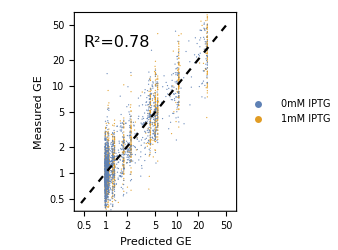

```mathematica
(* Plot the results for all promoters *)
predictionsRefinedEnergyMatrix={#[[Length@source+1;;]],#[[;;Length@source]]}&[Transpose@{fitRefinedEnergyMatrix["PredictedResponse"],fitRefinedEnergyMatrix["Response"]}];
leg=PointLegend[ColorData[97]/@Range@2,font/@{"0mM IPTG","1mM IPTG"},LegendFunction->frame,Spacings->{0.2,0.2}];
plot=Show[ListLogLogPlot[10^predictionsRefinedEnergyMatrix,FrameLabel->(font[#,14]&/@{"Predicted GE","Measured GE"})(*,PlotLabel->font["Bivalent RNAP Binding",14]*),PlotRange->{{10^-0.4,10^1.8},{10^-0.4,10^1.8}},AspectRatio->1,ImageSize->250,Epilog->{Text[font["R^2="<>ToString@rSqaured[Transpose@{fitRefinedEnergyMatrix["PredictedResponse"],fitRefinedEnergyMatrix["Response"]}],16],{Log[10^0.15],Log[10^1.5]}]},PlotLegends->Placed[leg,Scaled[{{0.77,0.18},{0.5,0.5}}]],PlotStyle->({ColorData[97][#],Opacity[0.9]}&/@{2,1}),Evaluate@opts],LogLogPlot[x,{x,10^-0.35,10^1.75},PlotStyle->{Black,Dashed}]]
```

```mathematica
Export["Predict_exp.pdf", %]
```

Predict_exp.pdf

#### Parameter Values

```mathematica
round=ReplacePart[ConstantArray[0.01,Length@bestFitParameters],{2->0.0001,4->0.001}];
parameterValues=List@@If[StringTake[ToString[#[[1]]],{-3,-1}]=="Log",StringTake[ToString[#[[1]]],{1,-4}]->E^(#[[2]]),ToString[#[[1]]]->#[[2]]]&/@Sort[bestFitParameters/.s_String/;StringMatchQ[s,"O"~~__]:>"lac"<>s];
parameterValues[[All,2]]=MapIndexed[Round[#,round[[First@#2]]]&,parameterValues[[All,2]]]/.{10.->∞};
parameterValues[[All,1]]=StringReplace[parameterValues[[All,1]],{"rMax"->"r_max","rMin"->"r_min","ϵ[minus10_"~~f__~~"]":>Row[{Subscript["E[-10",f],"]"}],"ϵ[minus35_"~~f__~~"]":>Row[{Subscript["E[-35",f],"]"}],"ϵ[lacO"~~num_~~"_"~~f__~~"]":>Row[{Subsuperscript["E[lac","O"<>num,f],"]"}],"ϵ[minus"~~num__~~"cons]":>Row[{Subscript["E[-"<>num,"cons"],"]"}],"ϵ[lacO"~~num_~~"]":>Row[{Subscript["E[lac","O"<>num],"]"}],"ϵ[lacOscram]":>Row[{Subscript["E[lac","Oscram"],"]"}],"ϵ[lacOsym]":>Row[{Subscript["E[lac","Osym"],"]"}]}]/.{StringExpression->Identity,"p"->"p_act^repressor","loop"->"E_loop"};
(* Rearrange parameters *)
parameterValues=Join[parameterValues[[{4,3,1,2}]],parameterValues[[5;;14]],parameterValues[[{18,17,15,16,22,19,20,21}]]];
parameterResults=Text@Grid[Prepend[parameterValues,Style[#,Bold]&/@{"Parameter","Value"}],Background->{None,{Lighter[Yellow,.9],Join[ConstantArray[RGBColor[0.8, 0.9, 0.9],{2}],ConstantArray[GrayLevel[1],{2}],ConstantArray[RGBColor[0.8, 0.9, 0.9],{10}],ConstantArray[GrayLevel[1],{4}],ConstantArray[RGBColor[0.8, 0.9, 0.9],{4}]]}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Center,Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Parameter | Value
r_min | 0.975
r_max | 31.26
E_loop | -3.05
p_act^repressor | 0.0047
(E[lac)_O1] | -0.39
(E[lac)_O1^rightSym] | 2.8
(E[lac)_O2] | 2.93
(E[lac)_O2^leftSym] | 4.73
(E[lac)_O2^rightSym] | 1.41
(E[lac)_O3] | 1.95
(E[lac)_O3^leftSym] | 3.21
(E[lac)_O3^rightSym] | 3.88
(E[lac)_Oscram] | ∞
(E[lac)_Osym] | -2.35
(E[-10)_cons] | 0.
(E[-10)_(7A)] | 3.93
(E[-10)_(12A)] | 4.93
(E[-10)_(12G)] | 3.69
(E[-35)_cons] | -1.82
(E[-35)_(30C_33T)] | 3.59
(E[-35)_(31A_32C)] | 0.75
(E[-35)_(33T)] | 1.77

```mathematica
Export["Model_weights.pdf", %]
```

Model_weights.pdf

### Predicting Leakiness and Saturation

#### Gene Expression as a Function of LacI Binding

```mathematica
formatM35[m35_]:=Subscript["-35",StringReplace[StringTake[m35,{If[StringTake[m35,{8,8}]==="_",9,8],-1}],"_"->","]]
formatM10[m10_]:=Subscript["-10",StringReplace[StringTake[m10,{If[StringTake[m10,{8,8}]==="_",9,8],-1}],"_"->","]]
fullResults[m35_,m10_,showPlotLabel_,showPlotLegend_]:=(
Zprox=E^(-(ϵprox-IPTG pLog))+E^(-(ϵprox+ϵdist-2IPTG pLog))+E^(-(ϵprox+ϵdist+loop-IPTG pLog));
ZnotProx=1+E^(-(ϵdist-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(ϵ[m35]+ϵ[m10]))Zprox)+E^rMaxLog E^(-(ϵ[m35]+ϵ[m10]))ZnotProx;
Zdenominator=(1+E^(-(ϵ[m35]+ϵ[m10])))(Zprox+ZnotProx);
fitFunction0mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->0;
fitFunction1mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->1;
(* Plot the inferred LacI binding energies from the experimental data versus its gene expression *)
plotData={{ϵ@#[[1]],ϵ@#[[4]],#[[-2]]}&/@Cases[source,{_,m35,m10,__}],{ϵ@#[[1]],ϵ@#[[4]],#[[-1]]}&/@Cases[source,{_,m35,m10,__}]}/.bestFitParameters;
With[{opts=Join[If[showPlotLabel,{PlotLabel->Row[Style[#,18]&/@{formatM35[m35],"/",formatM10[m10]}]},{}],If[showPlotLegend,{PlotLegends->Placed[{"0mM IPTG","1mM IPTG"},Below]},{}]]},
Show[Plot3D[{fitFunction0mMIPTG,fitFunction1mMIPTG},{ϵdist,-5,10},{ϵprox,-5,10},ScalingFunctions->"Log",PlotStyle->({ColorData[97][#],Opacity[0.5]}&/@Range@2),AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ViewPoint->{1.3,-2.9,1.2},AxesLabel->(font[#,If[showPlotLabel,18,20]]&/@{"ϵ_dist","ϵ_prox","GE"}),ImageSize->Medium,TicksStyle->Directive["Label",If[showPlotLabel,14,18]],PlotRange->{0.5,75.},opts],ListPointPlot3D[plotData,ScalingFunctions->"Log"](*,PlotRange->All*)]
]
)
```

Results for the -35_cons/-10_cons RNAP promoter. Un-comment the following line to see the results for the -35_(30,C,33,T)/-10_(12,A) promoter (and all other promoters can be seen by similarly modifying the code)

```mathematica
source
```

{{O2_leftSym,minus35_31A_32C,minus10_7A,lacO2,1.58109,2.26922},{O3_rightSym,minus35_33T,minus10_12G,O1_rightSym,0.932193,1.0258},{lacOsym,minus35_30C_33T,minus10cons,lacOsym,0.474488,0.796497},{lacOsym,minus35cons,minus10cons,O3_leftSym,6.03335,9.50744},{lacO3,minus35_30C_33T,minus10_12A,O3_rightSym,2.08422,1.21843},1477,{O2_rightSym,minus35_33T,minus10cons,lacO1,0.866406,2.57618},{O3_rightSym,minus35cons,minus10_12G,lacOsym,1.24578,8.09779},{O3_leftSym,minus35cons,minus10_12A,O3_rightSym,1.98891,2.5401},{O2_rightSym,minus35_31A_32C,minus10_7A,O1_rightSym,1.36692,1.47006}}
 |  |  |  |

```mathematica
fullResults["minus35cons","minus10cons",True,True]
(*fullResults["minus35_30C_33T","minus10_12A",True,True]*)
```

-Graphics3D-

Un-comment and run the following code if you want to see the resulting plots for all combinations of RNAP binding sites

```mathematica
Grid@Partition[fullResults[#[[1]],#[[2]],True,False]&/@Union@source[[All,{2,3}]],4]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Export["GE_grid_prom.pdf", %]
```

GE_grid_prom.pdf

```mathematica
ExpandFileName["GE_grid_prom.pdf"]
```

/Users/Leelu/GE_grid_prom.pdf

#### Fold-Change as a Function of LacI Binding

```mathematica
formatM35[m35_]:=Subscript["-35",StringReplace[StringTake[m35,{If[StringTake[m35,{8,8}]==="_",9,8],-1}],"_"->","]]
formatM10[m10_]:=Subscript["-10",StringReplace[StringTake[m10,{If[StringTake[m10,{8,8}]==="_",9,8],-1}],"_"->","]]
fullResultsFoldChange[m35_,m10_,showPlotLabel_,showPlotLegend_]:=(
Zprox=E^(-(ϵprox-IPTG pLog))+E^(-(ϵprox+ϵdist-2IPTG pLog))+E^(-(ϵprox+ϵdist+loop-IPTG pLog));
ZnotProx=1+E^(-(ϵdist-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(ϵ[m35]+ϵ[m10]))Zprox)+E^rMaxLog E^(-(ϵ[m35]+ϵ[m10]))ZnotProx;
Zdenominator=(1+E^(-(ϵ[m35]+ϵ[m10])))(Zprox+ZnotProx);
fitFunction0mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->0;
fitFunction1mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->1;
(* Plot the inferred LacI binding energies from the experimental data versus its gene expression *)
plotData={ϵ@#[[1]],ϵ@#[[4]],(#[[-1]])/(#[[-2]])}&/@Cases[source,{_,m35,m10,__}]/.bestFitParameters;
With[{opts=Join[If[showPlotLabel,{PlotLabel->Row[Style[#,18]&/@{formatM35[m35],"/",formatM10[m10]}]},{}],If[showPlotLegend,{PlotLegends->Placed[{"Fold Change"},Below]},{}]]},
Show[Plot3D[fitFunction1mMIPTG/fitFunction0mMIPTG,{ϵdist,-5,10},{ϵprox,-5,10},ScalingFunctions->"Log",PlotStyle->({ColorData[97][3],Opacity[0.5]}),AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ViewPoint->{1.3,-2.9,1.2},AxesLabel->(font[#,If[showPlotLabel,18,20]]&/@{"ϵ_dist","ϵ_prox","FC"}),ImageSize->Medium,TicksStyle->Directive["Label",If[showPlotLabel,14,18]],PlotRange->{0.5,20.},opts],ListPointPlot3D[plotData,ScalingFunctions->"Log",PlotStyle->ColorData[97][3]]]
]
)
```

Results for the -35_cons/-10_cons RNAP promoter. Un-comment the following line to see the results for the -35_(30,C,33,T)/-10_(12,A) promoter (and all other promoters can be seen by similarly modifying the code)

```mathematica
fullResultsFoldChange["minus35cons","minus10cons",True,True]
(*fullResultsFoldChange["minus35_30C_33T","minus10_12A",True,True]*)
```

-Graphics3D-

Un-comment and run the following code if you want to see the resulting plots for all combinations of RNAP binding sites

```mathematica
Grid@Partition[fullResultsFoldChange[#[[1]],#[[2]],True,False]&/@Union@source[[All,{2,3}]],4]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Export["FC_grid_prom.pdf", %]
```

FC_grid_prom.pdf